```mathematica
A11=B11=C11=D11=0;
```

```mathematica
A12=B12=C12=D12=0;
A13=B13=C13=D13=0;
G13=h13=0;
```

```mathematica
A01=B01=C01=D01=A02=B02=C02=D02=A03=B03=C03=D03=0
```

0

```mathematica
β=0;
```

# General Solution 1st Order

```mathematica
psi11=A01 y^3+B01 y^2+C01 y+D01+((A11+B11 y)Exp[-y]+(C11+D11 y)Exp[y])Cos[z]+((E11+F11 y)Exp[-y]+(G11+h11 y)Exp[y])Sin[z]
psi12=A02 Exp[-Sqrt[k]y]+B02 Exp[Sqrt[k]y]+C02 y+D02+((A12 Exp[-y]+B12 Exp[y]+C12 Exp[-y Sqrt[1+k]]+D12 Exp[y Sqrt[1+k]])Cos[z]+(E12 Exp[-y]+F12 Exp[y]+G12 Exp[-y Sqrt[1+k]]+h12 Exp[y Sqrt[1+k]])Sin[z])
psi13=A03 y^3+B03 y^2+C03 y+D03+((A13+B13 y)Exp[-y]+(C13+D13 y)Exp[y])Cos[z]+((E13+F13 y)Exp[-y]+(G13+h13 y)Exp[y])Sin[z]
```

(ⅇ^-y (E11+F11 y)+ⅇ^y (G11+h11 y)) Sin[z]

(ⅇ^-y E12+ⅇ^y F12+ⅇ^(-√(1+k) y) G12+ⅇ^(√(1+k) y) h12) Sin[z]

ⅇ^-y (E13+F13 y) Sin[z]

```mathematica
α=√(k+1)
```

√(1+k)

```mathematica
k=α^2-1;
H2=H1+δH
psi11=(E11 Cosh[y] +F11 Sinh[y] + (y) (G11 Cosh[y]+h11 Sinh[y])) Sin[z]
psi12=FullSimplify[( E12 Cosh[y-H2]+F12 Sinh[y-H2]- G12 2/k(Cosh[√(1+k)(y-H2)]-Cosh[(y-H2)])+2/k(Sinh[√(1+k)(y-H2)]-Sinh[(y-H2)]) h12) Sin[z],α>0]
psi13=ⅇ^(-(y-H2)) (E13+F13 (y-H2)) Sin[z]
```

H1+δH

Sin[z] (E11 Cosh[y]+F11 Sinh[y]+y (G11 Cosh[y]+h11 Sinh[y]))

(Sin[z] ((2 G12+E12 (-1+α^2)) Cosh[H1-y+δH]-2 G12 Cosh[α (H1-y+δH)]+(F12+2 h12-F12 α^2) Sinh[H1-y+δH]-2 h12 Sinh[α (H1-y+δH)]))/(-1+α^2)

ⅇ^(H1-y+δH) (E13+F13 (-H1+y-δH)) Sin[z]

# Pressure

```mathematica
Simplify[Integrate[Simplify[-D[psi11,y,y,y]-D[psi11,z,z,y]],z]]
```

2 Cos[z] (G11 Cosh[y]+h11 Sinh[y])

```mathematica
Simplify[Integrate[D[psi11,y,y,z]+D[psi11,z,z,z],y]]
```

2 Cos[z] (G11 Cosh[y]+h11 Sinh[y])

```mathematica
p11=2 Cos[z] (G11 Cosh[y]+h11 Sinh[y])
```

2 Cos[z] (G11 Cosh[y]+h11 Sinh[y])

```mathematica
Simplify[Integrate[-D[psi12,y,y,y]-D[psi12,z,z,y]+k D[psi12,y],z]]
```

-Cos[z] ((-2 h12+F12 (-1+α^2)) Cosh[H1-y+δH]+(E12-2 G12-E12 α^2) Sinh[H1-y+δH])

```mathematica
Simplify[Integrate[D[psi12,y,y,z]+D[psi12,z,z,z]-k D[psi12,z],y]]
```

-Cos[z] ((-2 h12+F12 (-1+α^2)) Cosh[H1-y+δH]+(E12-2 G12-E12 α^2) Sinh[H1-y+δH])

```mathematica
p12=-Cos[z] ((-2 h12+F12 (-1+α^2)) Cosh[H1-y+δH]+(E12-2 G12-E12 α^2) Sinh[H1-y+δH])
```

-Cos[z] ((-2 h12+F12 (-1+α^2)) Cosh[y-δH]-(E12-2 G12-E12 α^2) Sinh[y-δH])

```mathematica
Simplify[Integrate[-D[psi13,y,y,y]-D[psi13,z,z,y],z]]
```

2 ⅇ^(H1-y+δH) F13 Cos[z]

```mathematica
Simplify[Integrate[D[psi13,y,y,z]+D[psi13,z,z,z],y]]
```

2 ⅇ^(H1-y+δH) F13 Cos[z]

```mathematica
p13=2 ⅇ^(H1-y+δH) F13 Cos[z]
```

2 ⅇ^(-y+δH) F13 Cos[z]

## Verification

```mathematica
Simplify[(D[psi11,y,y,y,y]+D[psi11,z,z,z,z]+D[psi11,y,y,z,z]+D[psi11,y,y,z,z])]
```

0

```mathematica
Simplify[(D[psi12,y,y,y,y]+D[psi12,z,z,z,z]+D[psi12,y,y,z,z]+D[psi12,y,y,z,z])-k(D[psi12,y,y]+D[psi12,z,z])]
```

0

```mathematica
Simplify[(D[psi13,y,y,y,y]+D[psi13,z,z,z,z]+D[psi13,y,y,z,z]+D[psi13,y,y,z,z])]
```

0

# Preliminary Zeroth order

```mathematica
psi01=0;
psi02=0;
psi03=0;
```

# First Boundary Conditions

```mathematica
B1=Limit[D[psi11,y]+Sin[z]D[psi01,y,y],y->0];
```

```mathematica
b1=Collect[B1,{z,Sin[z],Cos[z]},FullSimplify]
```

B1

```mathematica
B2=Limit[D[psi11,z]+Sin[z]D[psi01,y,z]-Cos[z],y->0];
```

```mathematica
b2=Collect[B2,{z,Sin[z],Cos[z]},FullSimplify]
```

(-1+E11) Cos[z]

# Second Boundary Conditions

```mathematica
B3=Limit[D[psi11,y],y->H1]-Limit[D[psi12,y],y->H1];
```

```mathematica
Collect[B3,{z,Sin[z],Cos[z]},FullSimplify]
```

Sin[z] ((F11+G11+H1 h11) Cosh[H1]+((F12+2 h12-F12 α^2) Cosh[δH]-2 h12 α Cosh[α δH]+(E11+G11 H1+h11) (-1+α^2) Sinh[H1]-E12 Sinh[δH]+2 G12 Sinh[δH]+E12 α^2 Sinh[δH]-2 G12 α Sinh[α δH])/(-1+α^2))

```mathematica
B4=TrigReduce[Limit[D[psi11,z],y->H1]-Limit[D[psi12,z],y->H1]];
```

```mathematica
Collect[B4,{z,Sin[z],Cos[z]},FullSimplify]
```

(Cos[z] ((E11+G11 H1) (-1+α^2) Cosh[H1]+(E12-2 G12-E12 α^2) Cosh[δH]+2 G12 Cosh[α δH]+(F11+H1 h11) (-1+α^2) Sinh[H1]-(F12+2 h12) Sinh[δH]+F12 α^2 Sinh[δH]+2 h12 Sinh[α δH]))/(-1+α^2)

# Third Boundary Conditions

```mathematica
B5=Limit[D[psi11,y,y]-D[psi11,z,z],y->H1]-μ(Limit[D[psi12,y,y]-D[psi12,z,z],y->H1])+β Sqrt[μ k](Limit[D[psi12,y],y->H1]);
```

```mathematica
Collect[B5,{z,Sin[z],Cos[z]},FullSimplify]
```

-1/(2 (1+α) (-1+α^2))Sin[z] (-4 (-1+α) (1+α)^2 Cosh[H1]-4 h11 (-1+α) (1+α)^2 Cosh[H1]+2 (2 h12 (4+(1+α^2) μ (-4+(3+α) μ))-F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]-2 (2 h12 (2+μ (-4+(3+α) μ))+F12 (1+α) (2-μ (4+(-3+α^2) μ))) Cosh[α δH]-2 α^2 (2 h12 (2+μ (-4+(3+α) μ))+F12 (1+α) (2-μ (4+(-3+α^2) μ))) Cosh[α δH]-4 H1 (-1+α) (1+α)^2 (G11 Cosh[H1]+h11 Sinh[H1])+4 (1+α) (F12+2 h12-F12 α^2) μ Sinh[δH]-4 h12 (1+α) μ Sinh[α δH]-4 h12 α^2 (1+α) μ Sinh[α δH])

```mathematica
B6=Limit[p11+2D[psi11,y,z],y->H1]-μ(Limit[p12+2 D[psi12,y,z],y->H1]);
```

```mathematica
Collect[B6,{z,Sin[z],Cos[z]},FullSimplify]
```

Cos[z] (-2 h12 μ Cosh[δH]+F12 (-1+α^2) μ Cosh[δH]+2 (G11 Cosh[H1]+h11 Sinh[H1])+2 (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])-(h12 (4+(1+α^2) μ (-4+(3+α) μ)) Sinh[δH])/(1+α)+1/2 F12 (-4+(1+α^2) μ (4+(-3+α^2) μ)) Sinh[δH]-1/(-1+α^2)2 μ ((-2 h12+F12 (-1+α^2)) Cosh[δH]+2 h12 α Cosh[α δH]+((2 h12 (-4+(1+α^2) μ (4-(3+α) μ))+F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH])/(2 (1+α) μ)+(α ((2 h12 (2+μ (-4+(3+α) μ)))/(1+α)+F12 (2-μ (4+(-3+α^2) μ))) Sinh[α δH])/μ))

# Fourth Boundary Conditions

```mathematica
B7=TrigReduce[Limit[D[psi12,y],y->H2]-Limit[D[psi13,y],y->H2]];
```

```mathematica
Collect[B7,{z,Sin[z],Cos[z]},FullSimplify]
```

(E13+F12-F13+(2 h12)/(1+α)) Sin[z]

```mathematica
B8=TrigReduce[Limit[D[psi12,z],y->H2]-Limit[D[psi13,z],y->H2]];
```

```mathematica
Collect[B8,{z,Sin[z],Cos[z]},FullSimplify]
```

(E12-E13) Cos[z]

# Fifth Boundary Conditions

```mathematica
B9=TrigReduce[Limit[μ(D[psi12,y,y]-D[psi12,z,z]),y->H2]-(Limit[D[psi13,y,y]-D[psi13,z,z],y->H2])-β Sqrt[μ k](Limit[D[psi12,y],y->H2])];
```

```mathematica
Collect[B9,{z,Sin[z],Cos[z]},FullSimplify]
```

(-2 E13+2 F13+2 (E12-G12) μ-((F12+2 h12+F12 α) β √((-1+α^2) μ))/(1+α)) Sin[z]

```mathematica
B10=TrigReduce[Limit[μ(p12+2D[psi12,y,z]),y->H2]-(Limit[p13+2 D[psi13,y,z],y->H2])];
```

```mathematica
Collect[B10,{z,Sin[z],Cos[z]},FullSimplify]
```

(2 E13-4 F13+(2 h12 (3+α) μ)/(1+α)-F12 (-3+α^2) μ) Cos[z]

# Final Boundary Conditions

```mathematica
BF1=Collect[D[psi13,y]-U1,ⅇ^y,Simplify]
```

-U1-ⅇ^(-y+δH) (E13+F13 (-1+y-δH)) Sin[z]

```mathematica
BF2=Collect[D[psi13,z],ⅇ^y,Simplify]
```

ⅇ^(-y+δH) (E13+F13 (y-δH)) Cos[z]

# Solution

```mathematica
F11=-G11;
E11=1;
Collect[B1,{z,Sin[z],Cos[z]},FullSimplify]
Collect[B2,{z,Sin[z],Cos[z]},FullSimplify]
```

0

0

```mathematica
Collect[B10,{z,Sin[z],Cos[z]},FullSimplify]
```

(2 E13-4 F13+(2 h12 (3+α) μ)/(1+α)-F12 (-3+α^2) μ) Cos[z]

```mathematica
FullSimplify[Solve[{E13+F12-F13+(2 h12)/(1+α)==0,-2 E13+2 F13+2 (E12-G12) μ-((F12+2 h12+F12 α) β √((-1+α^2) μ))/(1+α)==0,2 E13-4 F13+(2 h12 (3+α) μ)/(1+α)-F12 (-3+α^2) μ==0},{E13,F13,G12}]]
```

{{E13→(h12 (-4+(3+α) μ))/(1+α)-1/2 F12 (4+(-3+α^2) μ),F13→(h12 (-2+(3+α) μ))/(1+α)-1/2 F12 (2+(-3+α^2) μ),G12→E12-((F12+2 h12+F12 α) (-2+β √((-1+α^2) μ)))/(2 (1+α) μ)}}

```mathematica
E12=E13;
E13=(h12 (-4+(3+α) μ))/(1+α)-1/2 F12 (4+(-3+α^2) μ);
F13=(h12 (-2+(3+α) μ))/(1+α)-1/2 F12 (2+(-3+α^2) μ);
G12=E12-((F12+2 h12+F12 α) (-2+β √((-1+α^2) μ)))/(2 (1+α) μ);
Collect[B7,{z,Sin[z],Cos[z]},FullSimplify]
Collect[B8,{z,Sin[z],Cos[z]},FullSimplify]
Collect[B9,{z,Sin[z],Cos[z]},FullSimplify]
Collect[B10,{z,Sin[z],Cos[z]},FullSimplify]
```

0

0

0

«1 more identical outputs»

```mathematica
Assuming[k>0&& μ>1,Collect[Expand[B3],{z,Sin[z],Cos[z]},FullSimplify]]
Assuming[k>0&& μ>1,Collect[Expand[B4],{z,Sin[z],Cos[z]},FullSimplify]]
Assuming[k>0&& μ>1,Collect[Expand[B5],{z,Sin[z],Cos[z]},FullSimplify]]
Assuming[k>0&& μ>1,Collect[Expand[B6],{z,Sin[z],Cos[z]},FullSimplify]]
```

```mathematica
B3=-1/(2 (-1+α) (1+α)^2 μ)(-2 H1 h11 (-1+α) (1+α)^2 μ Cosh[H1]+2 (1+α) (-2 h12+F12 (-1+α^2)) μ Cosh[δH]+4 h12 α μ Cosh[α δH]+4 h12 α^2 μ Cosh[α δH]-2 (1+G11 H1+h11) (-1+α) (1+α)^2 μ Sinh[H1]-4 F12 Sinh[δH]-8 h12 Sinh[δH]-4 F12 α Sinh[δH]+4 F12 μ Sinh[δH]+8 h12 μ Sinh[δH]+4 F12 α μ Sinh[δH]+4 F12 α^2 μ Sinh[δH]+8 h12 α^2 μ Sinh[δH]+4 F12 α^3 μ Sinh[δH]-3 F12 μ^2 Sinh[δH]-6 h12 μ^2 Sinh[δH]-3 F12 α μ^2 Sinh[δH]-2 h12 α μ^2 Sinh[δH]-2 F12 α^2 μ^2 Sinh[δH]-6 h12 α^2 μ^2 Sinh[δH]-2 F12 α^3 μ^2 Sinh[δH]-2 h12 α^3 μ^2 Sinh[δH]+F12 α^4 μ^2 Sinh[δH]+F12 α^5 μ^2 Sinh[δH]+2 F12 β √((-1+α^2) μ) Sinh[δH]+4 h12 β √((-1+α^2) μ) Sinh[δH]+2 F12 α β √((-1+α^2) μ) Sinh[δH]+4 F12 α Sinh[α δH]+8 h12 α Sinh[α δH]+4 F12 α^2 Sinh[α δH]-8 F12 α μ Sinh[α δH]-16 h12 α μ Sinh[α δH]-8 F12 α^2 μ Sinh[α δH]+6 F12 α μ^2 Sinh[α δH]+12 h12 α μ^2 Sinh[α δH]+6 F12 α^2 μ^2 Sinh[α δH]+4 h12 α^2 μ^2 Sinh[α δH]-2 F12 α^3 μ^2 Sinh[α δH]-2 F12 α^4 μ^2 Sinh[α δH]-2 F12 α β √((-1+α^2) μ) Sinh[α δH]-4 h12 α β √((-1+α^2) μ) Sinh[α δH]-2 F12 α^2 β √((-1+α^2) μ) Sinh[α δH]);
```

```mathematica
B4=1/(2 (-1+α) (1+α)^2 μ)(2 (1+G11 H1) (-1+α) (1+α)^2 μ Cosh[H1]+(-2 h12 (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F12 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]-2 ((-2 h12 (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))+F12 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))) Cosh[α δH]+(1+α) μ ((G11-H1 h11) (-1+α^2) Sinh[H1]+(F12+2 h12-F12 α^2) Sinh[δH]-2 h12 Sinh[α δH])));
```

```mathematica
B5=1/(2 (-1+α) (1+α)^2 μ)(4 (1+G11 H1+h11) (-1+α) (1+α)^2 μ Cosh[H1]+2 F12 β μ √((-1+α^2) μ) Cosh[δH]+4 h12 β μ √((-1+α^2) μ) Cosh[δH]+2 F12 α β μ √((-1+α^2) μ) Cosh[δH]-4 h12 α β μ √((-1+α^2) μ) Cosh[δH]+2 F12 α^2 β μ √((-1+α^2) μ) Cosh[δH]+2 F12 α^3 β μ √((-1+α^2) μ) Cosh[δH]+2 (1+α^2) (-2 h12 (3+α)+F12 (1+α) (-3+α^2)) μ^3 (Cosh[δH]-Cosh[α δH])-2 F12 β √((-1+α^2) μ^3) Cosh[α δH]-4 h12 β √((-1+α^2) μ^3) Cosh[α δH]-2 F12 α β √((-1+α^2) μ^3) Cosh[α δH]+4 h12 α β √((-1+α^2) μ^3) Cosh[α δH]-2 F12 α^2 β √((-1+α^2) μ^3) Cosh[α δH]-2 F12 α^3 β √((-1+α^2) μ^3) Cosh[α δH]+4 H1 h11 (-1+α) (1+α)^2 μ Sinh[H1]-4 F12 β √((-1+α^2) μ) Sinh[δH]-8 h12 β √((-1+α^2) μ) Sinh[δH]-4 F12 α β √((-1+α^2) μ) Sinh[δH]+4 F12 β √((-1+α^2) μ^3) Sinh[δH]+8 h12 β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α^2 β √((-1+α^2) μ^3) Sinh[δH]+8 h12 α^2 β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α^3 β √((-1+α^2) μ^3) Sinh[δH]-3 F12 β √((-1+α^2) μ^5) Sinh[δH]-6 h12 β √((-1+α^2) μ^5) Sinh[δH]-3 F12 α β √((-1+α^2) μ^5) Sinh[δH]-2 h12 α β √((-1+α^2) μ^5) Sinh[δH]-2 F12 α^2 β √((-1+α^2) μ^5) Sinh[δH]-6 h12 α^2 β √((-1+α^2) μ^5) Sinh[δH]-2 F12 α^3 β √((-1+α^2) μ^5) Sinh[δH]-2 h12 α^3 β √((-1+α^2) μ^5) Sinh[δH]+F12 α^4 β √((-1+α^2) μ^5) Sinh[δH]+F12 α^5 β √((-1+α^2) μ^5) Sinh[δH]+4 F12 α β √((-1+α^2) μ) Sinh[α δH]+8 h12 α β √((-1+α^2) μ) Sinh[α δH]+4 F12 α^2 β √((-1+α^2) μ) Sinh[α δH]-8 F12 α β √((-1+α^2) μ^3) Sinh[α δH]-16 h12 α β √((-1+α^2) μ^3) Sinh[α δH]-8 F12 α^2 β √((-1+α^2) μ^3) Sinh[α δH]+6 F12 α β √((-1+α^2) μ^5) Sinh[α δH]+12 h12 α β √((-1+α^2) μ^5) Sinh[α δH]+6 F12 α^2 β √((-1+α^2) μ^5) Sinh[α δH]+4 h12 α^2 β √((-1+α^2) μ^5) Sinh[α δH]-2 F12 α^3 β √((-1+α^2) μ^5) Sinh[α δH]-2 F12 α^4 β √((-1+α^2) μ^5) Sinh[α δH]+2 (F12+2 h12+F12 α) μ (-4 Cosh[δH]+2 (1+α^2) Cosh[α δH]+(-1+α^2) β^2 (Sinh[δH]-α Sinh[α δH]))+4 μ^2 (2 (F12+2 h12+F12 α) (1+α^2) Cosh[δH]-2 (F12+2 h12+F12 α) (1+α^2) Cosh[α δH]+(1+α) ((-2 h12+F12 (-1+α^2)) Sinh[δH]+h12 (1+α^2) Sinh[α δH])));
```

```mathematica
B6=1/(2 (-1+α) (1+α)^2) (4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]+2 (1+α) (-3+α^2) (-2 h12+F12 (-1+α^2)) μ Cosh[δH]-8 h12 α μ Cosh[α δH]-8 h12 α^2 μ Cosh[α δH]-4 (1+G11 H1+2 h11) Sinh[H1]-4 α Sinh[H1]-4 G11 H1 α Sinh[H1]-8 h11 α Sinh[H1]+4 α^2 Sinh[H1]+4 G11 H1 α^2 Sinh[H1]+8 h11 α^2 Sinh[H1]+4 α^3 Sinh[H1]+4 G11 H1 α^3 Sinh[H1]+8 h11 α^3 Sinh[H1]-6 F12 β √((-1+α^2) μ) Sinh[δH]-12 h12 β √((-1+α^2) μ) Sinh[δH]-6 F12 α β √((-1+α^2) μ) Sinh[δH]+2 F12 α^2 β √((-1+α^2) μ) Sinh[δH]+4 h12 α^2 β √((-1+α^2) μ) Sinh[δH]+2 F12 α^3 β √((-1+α^2) μ) Sinh[δH]+(-3+α^2) (2 h12 (-4+(1+α^2) μ (4-(3+α) μ))+F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]-8 F12 α Sinh[α δH]-16 h12 α Sinh[α δH]-8 F12 α^2 Sinh[α δH]+16 F12 α μ Sinh[α δH]+32 h12 α μ Sinh[α δH]+16 F12 α^2 μ Sinh[α δH]-12 F12 α μ^2 Sinh[α δH]-24 h12 α μ^2 Sinh[α δH]-12 F12 α^2 μ^2 Sinh[α δH]-8 h12 α^2 μ^2 Sinh[α δH]+4 F12 α^3 μ^2 Sinh[α δH]+4 F12 α^4 μ^2 Sinh[α δH]+4 F12 α β √((-1+α^2) μ) Sinh[α δH]+8 h12 α β √((-1+α^2) μ) Sinh[α δH]+4 F12 α^2 β √((-1+α^2) μ) Sinh[α δH]);
```

```mathematica
eqns=FullSimplify[{},k>0&& δH>0&& μ>1&& β ∈ Reals && H1>0];
```

## Full

```mathematica
full=Solve[{B3==0,B4==0,B5==0,B6==0},{F12,G11,h11,h12}];
```

```mathematica
Evaluate[Limit[h11/.full,α->1]]
```

$Aborted

```mathematica
U2=-((1+2 h11) √(-1+α^2) μ)/(2 √(-1+α^2) μ Cosh[√(-1+α^2) δH]+2 (-H1 (-1+α^2) (β^2-μ) μ-β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH]);
ux1=1/4 (-2-4 h11+((-1+ⅇ^(2 √(-1+α^2) δH)) H1 (1+2 h11) (-1+α^2) μ (-β^2+μ))/((√(-1+α^2)+H1 (-1+α^2) β^2+ⅇ^(2 √(-1+α^2) δH) (√(-1+α^2)-H1 (-1+α^2) β^2)) μ+(-1+ⅇ^(2 √(-1+α^2) δH)) H1 (-1+α^2) μ^2-(-1+ⅇ^(2 √(-1+α^2) δH)) β √((-1+α^2) μ)));
ux2=((1+2 h11) Sinh[1/2 √(-1+α^2) δH] (-((-1+α^2) μ Cosh[1/2 √(-1+α^2) δH])+√(-1+α^2) β √((-1+α^2) μ) Sinh[1/2 √(-1+α^2) δH]))/((-1+α^2) δH (√(-1+α^2) μ Cosh[√(-1+α^2) δH]+(-H1 (-1+α^2) (β^2-μ) μ-β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH]));
```

```mathematica
α=√(k+1)
```

√(1+k)

```mathematica
Clear[α]
```

### Validation plots

```mathematica
U[H1_,δH_,k_,β_,μ_]=Evaluate[U2/(1/2)/.full];
```

```mathematica
U[0.5,0.5,0.1,0,1]
```

{-0.975429}

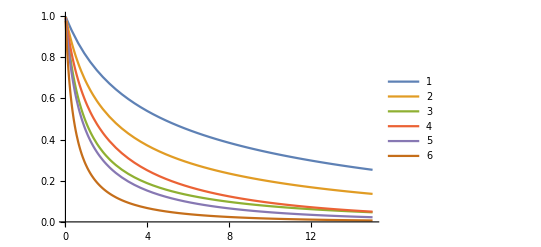

```mathematica
Plot[{U[0.5,0.5,k,0,1],U[1,0.5,k,0,1],U[2,0.5,k,0,1],U[0.5,1,k,0,1],U[1,1,k,0,1],U[2,1,k,0,1]},{k,0.01,15},PlotLegends->Automatic]
```

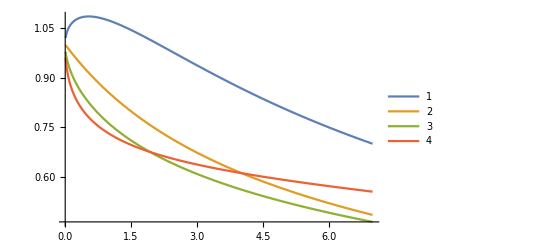

```mathematica
Plot[{U[0.3,0.5,k,0.5,1],U[0.3,0.5,k,0,1],U[0.3,0.5,k,-0.5,1],U[0.3,0.5,k,-1,1]},{k,0.01,7},PlotLegends->Automatic]
```

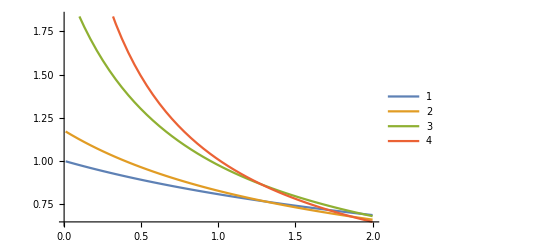

```mathematica
Plot[{U[0.5,0.5,k,0,1],U[0.5,0.5,k,0,2],U[0.5,0.5,k,0,5],U[0.5,0.5,k,0,10]},{k,0.01,2},PlotLegends->Automatic]
```

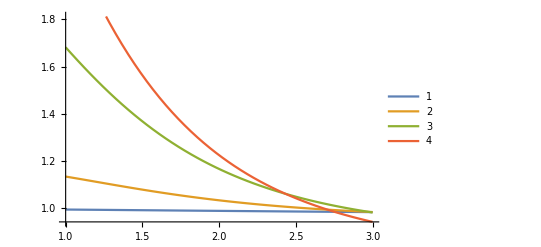

```mathematica
Plot[{U[H1,0.5,0.01,0,1],U[H1,0.5,0.01,0,2],U[H1,0.5,0.01,0,5],U[H1,0.5,0.01,0,10]},{H1,1,3},PlotLegends->Automatic]
```

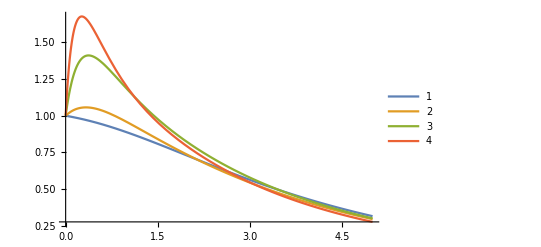

```mathematica
Plot[{U[1,δH,0.1,0,1],U[1,δH,0.1,0,2],U[1,δH,0.1,0,5],U[1,δH,0.1,0,10]},{δH,0,5},PlotLegends->Automatic]
```

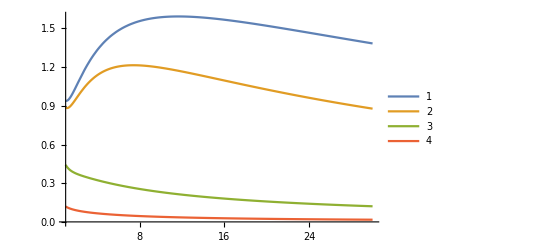

```mathematica
Plot[{U[1,1,0.05,0,μ],U[1,1,0.1,0,μ],U[1,1,1,0,μ],U[1,1,5,0,μ]},{μ,1,30},PlotLegends->Automatic]
```

```mathematica
Ux1[H1_,δH_,k_,β_,μ_]=Evaluate[ux1/(1/2)/.full];
```

```mathematica
Limit[Ux1[H1,δH,k,0,1],k->∞]
```

$Aborted

```mathematica
Ux1[H1,δH,k,0,1]
```

```mathematica
FullSimplify[N[Ux1[H1,1,100,0,1]]]
```

$Aborted

```mathematica
Limit[Ux1[0.5,0.5,k,0,1],k->∞]
```

{12.1061}

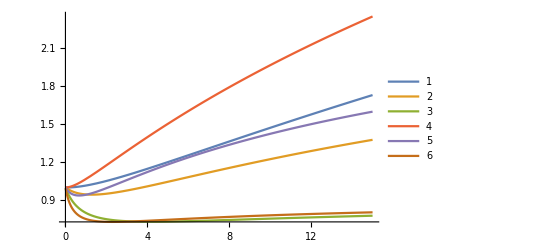

```mathematica
Plot[{Ux1[0.5,0.5,k,0,1],Ux1[1,0.5,k,0,1],Ux1[2,0.5,k,0,1],Ux1[0.5,1,k,0,1],Ux1[1,1,k,0,1],Ux1[2,1,k,0,1]},{k,0.01,15},PlotLegends->Automatic]
```

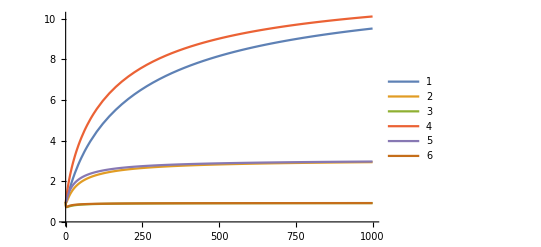

```mathematica
Plot[{Ux1[0.5,0.5,k,0,1],Ux1[1,0.5,k,0,1],Ux1[2,0.5,k,0,1],Ux1[0.5,1,k,0,1],Ux1[1,1,k,0,1],Ux1[2,1,k,0,1]},{k,0.01,1000},PlotLegends->Automatic]
```

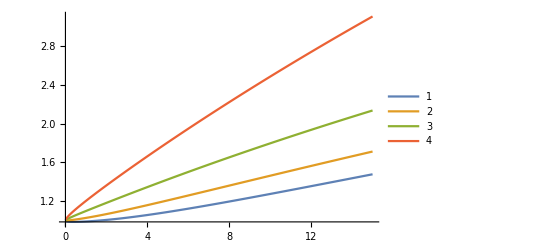

```mathematica
Plot[{Ux1[0.3,0.5,k,0.5,1],Ux1[0.3,0.5,k,0,1],Ux1[0.3,0.5,k,-0.5,1],Ux1[0.3,0.5,k,-1,1]},{k,0.01,15},PlotLegends->Automatic]
```

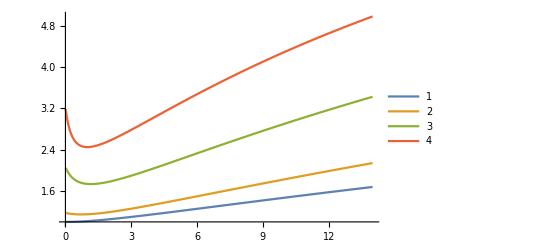

```mathematica
Plot[{Ux1[0.5,0.5,k,0,1],Ux1[0.5,0.5,k,0,2],Ux1[0.5,0.5,k,0,5],Ux1[0.5,0.5,k,0,10]},{k,0.01,14},PlotLegends->Automatic]
```

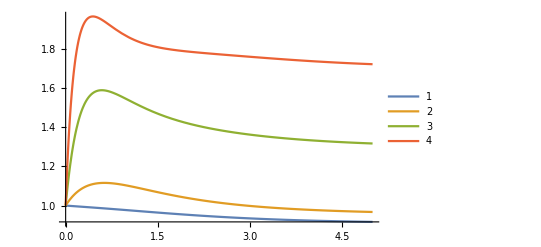

```mathematica
Plot[{Ux1[1,δH,0.1,0,1],Ux1[1,δH,0.1,0,2],Ux1[1,δH,0.1,0,5],Ux1[1,δH,0.1,0,10]},{δH,0,5},PlotLegends->Automatic]
```

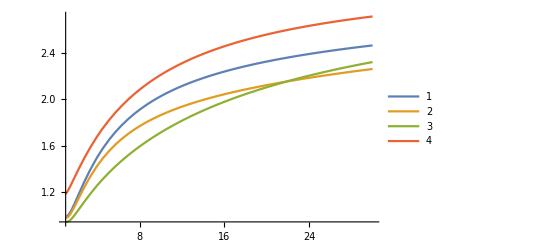

```mathematica
Plot[{Ux1[1,1,0.05,0,μ],Ux1[1,1,0.1,0,μ],Ux1[1,1,1,0,μ],Ux1[1,1,5,0,μ]},{μ,1,30},PlotLegends->Automatic]
```

```mathematica
Ux2[H1_,δH_,k_,β_,μ_]=Evaluate[ux2 /(1/2)/.full];
```

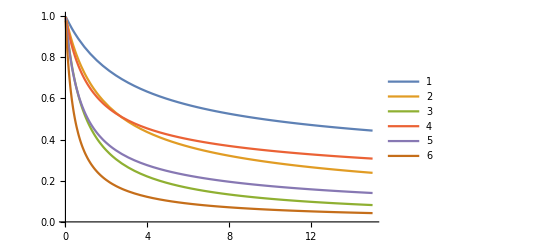

```mathematica
Plot[{Ux2[0.5,0.5,k,0,1],Ux2[1,0.5,k,0,1],Ux2[2,0.5,k,0,1],Ux2[0.5,1,k,0,1],Ux2[1,1,k,0,1],Ux2[2,1,k,0,1]},{k,0.01,15},PlotLegends->Automatic]
```

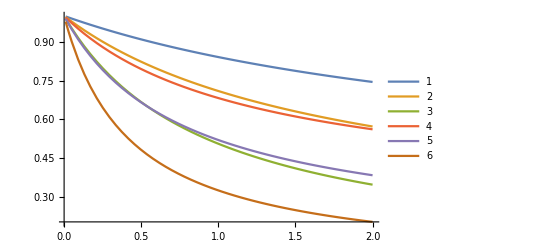

```mathematica
Plot[{Ux2[0.5,0.5,k,0,1],Ux2[1,0.5,k,0,1],Ux2[2,0.5,k,0,1],Ux2[0.5,1,k,0,1],Ux2[1,1,k,0,1],Ux2[2,1,k,0,1]},{k,0.01,2},PlotLegends->Automatic]
```

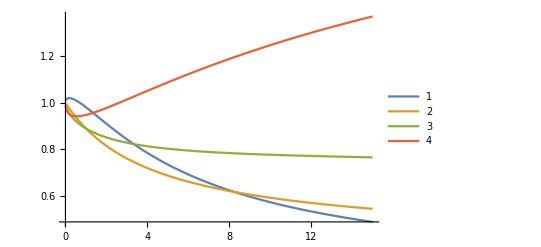

```mathematica
Plot[{Ux2[0.3,0.5,k,0.5,1],Ux2[0.3,0.5,k,0,1],Ux2[0.3,0.5,k,-0.5,1],Ux2[0.3,0.5,k,-1,1]},{k,0.01,15},PlotLegends->Automatic]
```

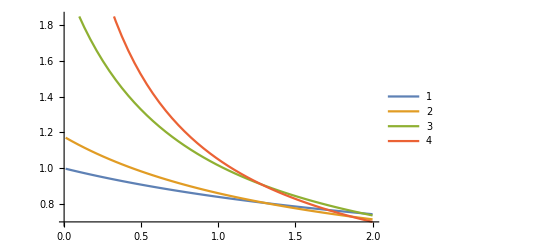

```mathematica
Plot[{Ux2[0.5,0.5,k,0,1],Ux2[0.5,0.5,k,0,2],Ux2[0.5,0.5,k,0,5],Ux2[0.5,0.5,k,0,10]},{k,0.01,2},PlotLegends->Automatic]
```

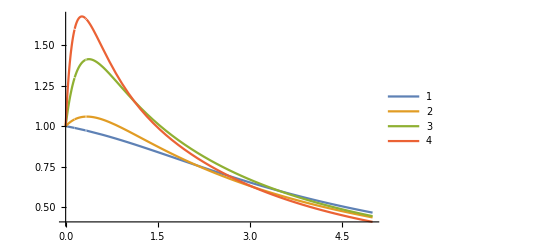

```mathematica
Plot[{Ux2[1,δH,0.1,0,1],Ux2[1,δH,0.1,0,2],Ux2[1,δH,0.1,0,5],Ux2[1,δH,0.1,0,10]},{δH,0,5},PlotLegends->Automatic]
```

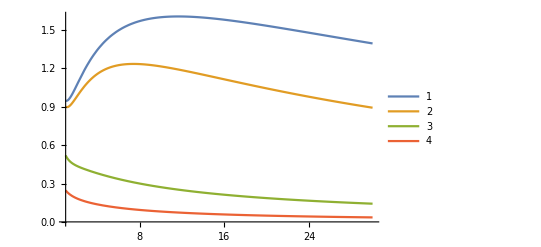

```mathematica
Plot[{Ux2[1,1,0.05,0,μ],Ux2[1,1,0.1,0,μ],Ux2[1,1,1,0,μ],Ux2[1,1,5,0,μ]},{μ,1,30},PlotLegends->Automatic]
```

## Brinkman flow

```mathematica
H1=0;
β=0;
μ=1;
```

```mathematica
full=Solve[{B3==0,B4==0,B5==0,B6==0},{F12,G11,h11,h12}];
```

```mathematica
full
```

{{F12→-((-(2 Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(2 √(1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 (1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(3 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(√(1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 √(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 (1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2))/(-((((-4+(2+k2 δH^-n)^2) Cosh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(k2 δH^-n Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-Sinh[δH]/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))) ((2 Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(2 √(1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 (1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(3 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(√(1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 √(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 (1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)))+(-(k2 δH^-n Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(3 Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(3 √(1+k2 δH^-n) Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^2 Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(5/2) Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(√(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^(3/2) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^2 Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)) (-((4+(2+k2 δH^-n) (-1+√(1+k2 δH^-n))) Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(2 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(2 Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))))),G11→-((δH^-n (-2 k2 δH^n Cosh[δH]+4 δH^(2 n) Cosh[δH]-2 k2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]+4 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH]-4 k2 δH^n Cosh[δH √(1+k2 δH^-n)]-4 δH^(2 n) Cosh[δH √(1+k2 δH^-n)]-4 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]+k2^2 Sinh[δH]-4 k2 δH^n Sinh[δH]+4 δH^(2 n) Sinh[δH]-k2^2 √(δH^-n (k2+δH^n)) Sinh[δH]+4 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH]-4 k2 δH^n Sinh[δH √(1+k2 δH^-n)]-4 δH^(2 n) Sinh[δH √(1+k2 δH^-n)]-4 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]))/(2 (-k2 Cosh[δH]+2 δH^n Cosh[δH]+k2 √(δH^-n (k2+δH^n)) Cosh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]-2 δH^n Cosh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]+2 δH^n Sinh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]-2 δH^n Sinh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)])))+(δH^(-3 n) (-(2 Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(2 √(1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 (1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(3 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(√(1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 √(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 (1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)) (-4 k2^3 δH^n Cosh[δH]^2+4 k2^2 δH^(2 n) Cosh[δH]^2+8 k2 δH^(3 n) Cosh[δH]^2-2 k2^3 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]^2+8 k2 δH^(3 n) √(δH^-n (k2+δH^n)) Cosh[δH]^2-4 k2^3 δH^n Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-20 k2^2 δH^(2 n) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-16 k2 δH^(3 n) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-2 k2^3 δH^n √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-12 k2^2 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-16 k2 δH^(3 n) √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]+8 k2^2 δH^(2 n) Cosh[δH √(1+k2 δH^-n)]^2+8 k2 δH^(3 n) Cosh[δH √(1+k2 δH^-n)]^2+4 k2^2 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]^2+8 k2 δH^(3 n) √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]^2-4 k2^3 δH^n Cosh[δH √(1+k2 δH^-n)] Sinh[δH]-4 k2^2 δH^(2 n) Cosh[δH √(1+k2 δH^-n)] Sinh[δH]-2 k2^3 δH^n √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)] Sinh[δH]-4 k2^2 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)] Sinh[δH]+4 k2^3 δH^n Sinh[δH]^2-4 k2^2 δH^(2 n) Sinh[δH]^2-8 k2 δH^(3 n) Sinh[δH]^2+2 k2^3 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]^2-8 k2 δH^(3 n) √(δH^-n (k2+δH^n)) Sinh[δH]^2-6 k2^3 δH^n Cosh[δH] Sinh[δH √(1+k2 δH^-n)]-12 k2^2 δH^(2 n) Cosh[δH] Sinh[δH √(1+k2 δH^-n)]-12 k2^2 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH] Sinh[δH √(1+k2 δH^-n)]-k2^4 Sinh[δH] Sinh[δH √(1+k2 δH^-n)]-4 k2^3 δH^n Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+4 k2^2 δH^(2 n) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+16 k2 δH^(3 n) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]-2 k2^3 δH^n √(δH^-n (k2+δH^n)) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]-4 k2^2 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+16 k2 δH^(3 n) √(δH^-n (k2+δH^n)) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]-8 k2^2 δH^(2 n) Sinh[δH √(1+k2 δH^-n)]^2-8 k2 δH^(3 n) Sinh[δH √(1+k2 δH^-n)]^2-4 k2^2 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]^2-8 k2 δH^(3 n) √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]^2))/(2 (-1+√(δH^-n (k2+δH^n))) (1+√(δH^-n (k2+δH^n)))^2 (-k2 Cosh[δH]+2 δH^n Cosh[δH]+k2 √(δH^-n (k2+δH^n)) Cosh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]-2 δH^n Cosh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]+2 δH^n Sinh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]-2 δH^n Sinh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]) (-((((-4+(2+k2 δH^-n)^2) Cosh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(k2 δH^-n Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-Sinh[δH]/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))) ((2 Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(2 √(1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 (1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(3 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(√(1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 √(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 (1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)))+(-(k2 δH^-n Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(3 Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(3 √(1+k2 δH^-n) Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^2 Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(5/2) Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(√(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^(3/2) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^2 Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)) (-((4+(2+k2 δH^-n) (-1+√(1+k2 δH^-n))) Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(2 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(2 Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))))),h11→-((k2 (1+√(δH^-n (k2+δH^n))) (Cosh[δH √(1+k2 δH^-n)]+Sinh[δH √(1+k2 δH^-n)]))/(-k2 Cosh[δH]+2 δH^n Cosh[δH]+k2 √(δH^-n (k2+δH^n)) Cosh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]-2 δH^n Cosh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]+2 δH^n Sinh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]-2 δH^n Sinh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]))+(k2^2 δH^(-2 n) (-(2 Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(2 √(1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 (1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(3 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(√(1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 √(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 (1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)) (2 k2 Cosh[δH] Cosh[δH √(1+k2 δH^-n)]+2 δH^n Cosh[δH] Cosh[δH √(1+k2 δH^-n)]+2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]+k2 Cosh[δH] Sinh[δH √(1+k2 δH^-n)]+4 δH^n Cosh[δH] Sinh[δH √(1+k2 δH^-n)]+k2 √(δH^-n (k2+δH^n)) Cosh[δH] Sinh[δH √(1+k2 δH^-n)]+4 δH^n √(δH^-n (k2+δH^n)) Cosh[δH] Sinh[δH √(1+k2 δH^-n)]+2 δH^n Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]))/(2 (-1+√(δH^-n (k2+δH^n))) (1+√(δH^-n (k2+δH^n))) (-k2 Cosh[δH]+2 δH^n Cosh[δH]+k2 √(δH^-n (k2+δH^n)) Cosh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]-2 δH^n Cosh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]+2 δH^n Sinh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]-2 δH^n Sinh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]) (-((((-4+(2+k2 δH^-n)^2) Cosh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(k2 δH^-n Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-Sinh[δH]/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))) ((2 Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(2 √(1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 (1+k2 δH^-n) Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(3 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(√(1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 √(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(2 (1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)))+(-(k2 δH^-n Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(3 Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(3 √(1+k2 δH^-n) Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(3/2) Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^2 Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n)^(5/2) Sinh[δH])/(2 (-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-(√(1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)-((1+k2 δH^-n) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^(3/2) Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+((1+k2 δH^-n)^2 Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)) (-((4+(2+k2 δH^-n) (-1+√(1+k2 δH^-n))) Cosh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n))^2)+(2 Cosh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))-(2 Sinh[δH])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))+(2 Sinh[δH √(1+k2 δH^-n)])/((-1+√(1+k2 δH^-n)) (1+√(1+k2 δH^-n)))))),h12→-((δH^n (-1+√(δH^-n (k2+δH^n))) (1+√(δH^-n (k2+δH^n)))^2 (2 δH^n Cosh[δH]+2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]+k2 Sinh[δH]+4 δH^n Sinh[δH]+k2 √(δH^-n (k2+δH^n)) Sinh[δH]+4 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]-2 k2 Sinh[δH √(1+k2 δH^-n)]-2 δH^n Sinh[δH √(1+k2 δH^-n)]-2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]))/(2 (4 k2 δH^n Cosh[δH]^2+4 δH^(2 n) Cosh[δH]^2+2 k2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH]^2+4 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH]^2-2 k2^2 Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-10 k2 δH^n Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-8 δH^(2 n) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-k2^2 √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-6 k2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]-8 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH] Cosh[δH √(1+k2 δH^-n)]+4 k2 δH^n Cosh[δH √(1+k2 δH^-n)]^2+4 δH^(2 n) Cosh[δH √(1+k2 δH^-n)]^2+2 k2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]^2+4 δH^(2 n) √(δH^-n (k2+δH^n)) Cosh[δH √(1+k2 δH^-n)]^2-4 k2 δH^n Sinh[δH]^2-4 δH^(2 n) Sinh[δH]^2-2 k2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH]^2-4 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH]^2-2 k2^2 Cosh[δH] Sinh[δH √(1+k2 δH^-n)]-4 k2 δH^n Cosh[δH] Sinh[δH √(1+k2 δH^-n)]-4 k2 δH^n √(δH^-n (k2+δH^n)) Cosh[δH] Sinh[δH √(1+k2 δH^-n)]+k2^2 Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+6 k2 δH^n Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+8 δH^(2 n) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+2 k2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]+8 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH] Sinh[δH √(1+k2 δH^-n)]-4 k2 δH^n Sinh[δH √(1+k2 δH^-n)]^2-4 δH^(2 n) Sinh[δH √(1+k2 δH^-n)]^2-2 k2 δH^n √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]^2-4 δH^(2 n) √(δH^-n (k2+δH^n)) Sinh[δH √(1+k2 δH^-n)]^2)))}}

```mathematica
Clear[α]
```

```mathematica
U2=FullSimplify[-((1+2 h11) √(-1+α^2) μ)/(2 √(-1+α^2) μ Cosh[√(-1+α^2) δH]+2 (-H1 (-1+α^2) (β^2-μ) μ-β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH])]
ux1=FullSimplify[1/4 (-2-4 h11+((-1+ⅇ^(2 √(-1+α^2) δH)) H1 (1+2 h11) (-1+α^2) μ (-β^2+μ))/((√(-1+α^2)+H1 (-1+α^2) β^2+ⅇ^(2 √(-1+α^2) δH) (√(-1+α^2)-H1 (-1+α^2) β^2)) μ+(-1+ⅇ^(2 √(-1+α^2) δH)) H1 (-1+α^2) μ^2-(-1+ⅇ^(2 √(-1+α^2) δH)) β √((-1+α^2) μ)))]
ux2=FullSimplify[((1+2 h11) Sinh[1/2 √(-1+α^2) δH] (-((-1+α^2) μ Cosh[1/2 √(-1+α^2) δH])+√(-1+α^2) β √((-1+α^2) μ) Sinh[1/2 √(-1+α^2) δH]))/((-1+α^2) δH (√(-1+α^2) μ Cosh[√(-1+α^2) δH]+(-H1 (-1+α^2) (β^2-μ) μ-β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH]))]
```

-1/2 (1+2 h11) Sech[√(-1+α^2) δH]

-1/2-h11

-((1+2 h11) Tanh[√(-1+α^2) δH])/(2 √(-1+α^2) δH)

```mathematica
√(-1+(α)^2) δH
```

```mathematica
α=√(k^2+1)
```

√(1+k2^2 δH^(-2 n))

```mathematica
FullSimplify[√(-1+k^2+1),k>0]
```

k

```mathematica
k=k2/δH^n
```

k2 δH^-n

```mathematica
FullSimplify[Sech[√(-1+α^2) δH],k2>0 &&δH>0]
```

Sech[k2 δH^(1-n)]

```mathematica
Assuming[n>1,Limit[Sech[k2 δH^(1-n)],δH->∞]]
```

1

```mathematica
FullSimplify[-((1+2 h11) Tanh[√(-1+α^2) δH])/(2 √(-1+α^2) δH),k2>0 &&δH>0]
```

-((1+2 h11) δH^(-1+n) Tanh[k2 δH^(1-n)])/(2 k2)

```mathematica
Assuming[n>1,Limit[-((1+2 h11) δH^(-1+n) Tanh[k2 δH^(1-n)])/(2 k2),δH->∞]]
```

-1/2-h11

```mathematica
√(1+k^2)
```

√(1+k2^2 δH^(-2 n))

```mathematica
Clear[α]
```

```mathematica
FullSimplify[h11/.full]
```

{-((-1+α^2) (2 α+2 α Cosh[α δH] Sinh[δH]+(2 Cosh[δH]+(3+α^2) Sinh[δH]) Sinh[α δH]))/(-8 α+2 α (3+α^2) Cosh[δH] Cosh[α δH]+2 (2 (-1+α^2) Cosh[δH]-(3+α^2) Sinh[δH]) Sinh[α δH])}

```mathematica
FullSimplify[(h11-1/2 (-1-α))/.full]
```

{(α (1+α) ((3+α^2) Cosh[δH-α δH]-2 (1+α+(-1+α) Sinh[δH-α δH])))/(-8 α+2 α (3+α^2) Cosh[δH] Cosh[α δH]+2 (2 (-1+α^2) Cosh[δH]-(3+α^2) Sinh[δH]) Sinh[α δH])}

```mathematica
Limit[{(α (1+α) ((3+α^2) Cosh[δH-α δH]-2 (1+α+(-1+α) Sinh[δH-α δH])))/(-8 α+2 α (3+α^2) Cosh[δH] Cosh[α δH]+2 (2 (-1+α^2) Cosh[δH]-(3+α^2) Sinh[δH]) Sinh[α δH])},δH->∞]
```

{ConditionalExpression[0, 1<α<2]}

```mathematica
FullSimplify[(α (1+α) ((3+α^2) Cosh[δH-α δH]-2 (1+α+(-1+α) Sinh[δH-α δH])))/(-8 α+2 α (3+α^2) Cosh[δH] Cosh[α δH]+2 (2 (-1+α^2) Cosh[δH]-(3+α^2) Sinh[δH]) Sinh[α δH])]
```

(√(1+k2^2 δH^(-2 n)) (1+√(1+k2^2 δH^(-2 n))) ((4+k2^2 δH^(-2 n)) Cosh[δH-δH √(1+k2^2 δH^(-2 n))]-2 (1+√(1+k2^2 δH^(-2 n))+(-1+√(1+k2^2 δH^(-2 n))) Sinh[δH-δH √(1+k2^2 δH^(-2 n))])))/(-8 √(1+k2^2 δH^(-2 n))+2 √(1+k2^2 δH^(-2 n)) (4+k2^2 δH^(-2 n)) Cosh[δH] Cosh[δH √(1+k2^2 δH^(-2 n))]-2 δH^(-2 n) (-2 k2^2 Cosh[δH]+(k2^2+4 δH^(2 n)) Sinh[δH]) Sinh[δH √(1+k2^2 δH^(-2 n))])

```mathematica
Assuming[n>1,Limit[(√(1+k2^2 δH^(-2 n)) (1+√(1+k2^2 δH^(-2 n))) ((4+k2^2 δH^(-2 n)) Cosh[δH-δH √(1+k2^2 δH^(-2 n))]-2 (1+√(1+k2^2 δH^(-2 n))+(-1+√(1+k2^2 δH^(-2 n))) Sinh[δH-δH √(1+k2^2 δH^(-2 n))])))/(-8 √(1+k2^2 δH^(-2 n))+2 √(1+k2^2 δH^(-2 n)) (4+k2^2 δH^(-2 n)) Cosh[δH] Cosh[δH √(1+k2^2 δH^(-2 n))]-2 δH^(-2 n) (-2 k2^2 Cosh[δH]+(k2^2+4 δH^(2 n)) Sinh[δH]) Sinh[δH √(1+k2^2 δH^(-2 n))]),δH->∞]]
```

ConditionalExpression[0, k2^2∈ℝ]

## Slip flow

```mathematica
Series[U[H1,δH,k,0,1],{δH,∞,0}]//Normal
Series[Ux1[H1,δH,k,0,1],{δH,∞,0}]//Normal
Series[Ux2[H1,δH,k,0,1],{δH,∞,0}]//Normal
```

$Aborted

$Aborted

$Aborted

```mathematica
Assuming[k>0,Limit[Limit[U[H1,δH,k,0,1],H1->0],δH->∞]]
Assuming[k>0,Limit[Limit[Ux1[H1,δH,k,0,1],H1->0],δH->∞]]
Assuming[k>0,Limit[Limit[Ux2[H1,δH,k,0,1],H1->0],δH->∞]]
```

{ConditionalExpression[0, 3/2<√(1+k)<5/3]}

{ConditionalExpression[(k^3+32 (1+√(1+k))+16 k (3+2 √(1+k))+k^2 (17+5 √(1+k)))/((1+√(1+k))^3 (6+k+2 √(1+k))), 3/2<√(1+k)<5/3]}

{ConditionalExpression[0, 3/2<√(1+k)<5/3]}

```mathematica
FullSimplify[Series[U[H1,δH,k,0,μ],{k,0,0}]//Normal]
FullSimplify[Series[Ux1[H1,δH,k,0,μ],{k,0,0}]//Normal]
FullSimplify[Series[Ux2[H1,δH,k,0,μ],{k,0,0}]//Normal]
```

{(2+4 δH^2-16 H1 δH (-1+μ)^2 μ+4 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-2 μ (μ^3+2 δH^2 (4-4 μ+μ^3))-2 (-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-4 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+2 Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (1+2 δH^2+8 H1 δH (-1+μ)^2 μ-μ^2 (2 δH^2 (-2+μ)^2+μ^2)-2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH])+Cosh[2 δH] ((-1+μ) (1+2 H1^2 (-1+μ)+μ) (1+μ^2)-4 μ^2 Sinh[2 H1])+2 μ ((-1+μ) (1+2 H1^2 (-1+μ)+μ)-ⅇ^(2 H1) (1+μ^2)) Sinh[2 δH]))}

{(2+4 δH^2-16 H1 δH (-1+μ)^2 μ+4 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-2 μ (μ^3+2 δH^2 (4-4 μ+μ^3))-2 (-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-4 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+2 Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (1+2 δH^2+8 H1 δH (-1+μ)^2 μ-μ^2 (2 δH^2 (-2+μ)^2+μ^2)-2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH])+Cosh[2 δH] ((-1+μ) (1+2 H1^2 (-1+μ)+μ) (1+μ^2)-4 μ^2 Sinh[2 H1])+2 μ ((-1+μ) (1+2 H1^2 (-1+μ)+μ)-ⅇ^(2 H1) (1+μ^2)) Sinh[2 δH]))}

{(2+4 δH^2-16 H1 δH (-1+μ)^2 μ+4 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-2 μ (μ^3+2 δH^2 (4-4 μ+μ^3))-2 (-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-4 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+2 Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (1+2 δH^2+8 H1 δH (-1+μ)^2 μ-μ^2 (2 δH^2 (-2+μ)^2+μ^2)-2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH])+Cosh[2 δH] ((-1+μ) (1+2 H1^2 (-1+μ)+μ) (1+μ^2)-4 μ^2 Sinh[2 H1])+2 μ ((-1+μ) (1+2 H1^2 (-1+μ)+μ)-ⅇ^(2 H1) (1+μ^2)) Sinh[2 δH]))}

```mathematica
Limit[(2+4 δH^2-16 H1 δH (-1+μ)^2 μ+4 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-2 μ (μ^3+2 δH^2 (4-4 μ+μ^3))-2 (-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-4 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+2 Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (1+2 δH^2+8 H1 δH (-1+μ)^2 μ-μ^2 (2 δH^2 (-2+μ)^2+μ^2)-2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH])+Cosh[2 δH] ((-1+μ) (1+2 H1^2 (-1+μ)+μ) (1+μ^2)-4 μ^2 Sinh[2 H1])+2 μ ((-1+μ) (1+2 H1^2 (-1+μ)+μ)-ⅇ^(2 H1) (1+μ^2)) Sinh[2 δH])),δH->∞]
Limit[(2+4 δH^2-16 H1 δH (-1+μ)^2 μ+4 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-2 μ (μ^3+2 δH^2 (4-4 μ+μ^3))-2 (-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-4 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+2 Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (1+2 δH^2+8 H1 δH (-1+μ)^2 μ-μ^2 (2 δH^2 (-2+μ)^2+μ^2)-2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH])+Cosh[2 δH] ((-1+μ) (1+2 H1^2 (-1+μ)+μ) (1+μ^2)-4 μ^2 Sinh[2 H1])+2 μ ((-1+μ) (1+2 H1^2 (-1+μ)+μ)-ⅇ^(2 H1) (1+μ^2)) Sinh[2 δH])),δH->∞]
```

ConditionalExpression[-((-1+2 H1^2 (-1+μ)-μ) (-1+μ)+(1+μ^2) Cosh[2 H1]+2 μ Sinh[2 H1])/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1]), (H1|(-1+μ)^2|μ)∈ℝ]

ConditionalExpression[-((-1+2 H1^2 (-1+μ)-μ) (-1+μ)+(1+μ^2) Cosh[2 H1]+2 μ Sinh[2 H1])/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1]), (H1|(-1+μ)^2|μ)∈ℝ]

```mathematica
FullSimplify[-((-1+2 H1^2 (-1+μ)-μ) (-1+μ)+(1+μ^2) Cosh[2 H1]+2 μ Sinh[2 H1])/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1])]
FullSimplify[-((-1+2 H1^2 (-1+μ)-μ) (-1+μ)+(1+μ^2) Cosh[2 H1]+2 μ Sinh[2 H1])/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1])]
```

1-(4 H1^2 (-1+μ)^2)/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1])

1-(4 H1^2 (-1+μ)^2)/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1])

```mathematica
Series[1-(4 H1^2 (-1+μ)^2)/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1]),{H1,0,2}]
```

1+2 (-1+μ)^2 H1^2+O[H1]^3

```mathematica
Limit[(2+4 δH^2-16 H1 δH (-1+μ)^2 μ+4 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-2 μ (μ^3+2 δH^2 (4-4 μ+μ^3))-2 (-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-4 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+2 Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (1+2 δH^2+8 H1 δH (-1+μ)^2 μ-μ^2 (2 δH^2 (-2+μ)^2+μ^2)-2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH])+Cosh[2 δH] ((-1+μ) (1+2 H1^2 (-1+μ)+μ) (1+μ^2)-4 μ^2 Sinh[2 H1])+2 μ ((-1+μ) (1+2 H1^2 (-1+μ)+μ)-ⅇ^(2 H1) (1+μ^2)) Sinh[2 δH])),δH->∞]
```

ConditionalExpression[-((-1+2 H1^2 (-1+μ)-μ) (-1+μ)+(1+μ^2) Cosh[2 H1]+2 μ Sinh[2 H1])/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1]), (H1|(-1+μ)^2|μ)∈ℝ]

```mathematica
FullSimplify[Series[-((-1+2 H1^2 (-1+μ)-μ) (-1+μ)+(1+μ^2) Cosh[2 H1]+2 μ Sinh[2 H1])/((-1+μ) (1+2 H1^2 (-1+μ)+μ)-(1+μ^2) Cosh[2 H1]-2 μ Sinh[2 H1]),{H1,0,2}]]
```

1+2 (-1+μ)^2 H1^2+O[H1]^3

## μ=1 β=0

```mathematica
μ=1;
β=0;
FullSimplify[eqns,k>0&& δH>0&& β ∈ Reals && H1>0]
```

{(1+α) (-2 H1 h11 (-1+α^2) Cosh[H1]-2 (F12+2 h12-F12 α^2) Cosh[δH]+4 h12 α Cosh[α δH]-2 (1+G11 H1+h11) (-1+α^2) Sinh[H1]-3 F12 Sinh[δH]-6 h12 Sinh[δH]+4 h12 α Sinh[δH]+2 F12 α^2 Sinh[δH]-2 h12 α^2 Sinh[δH]+F12 α^4 Sinh[δH]+2 F12 α Sinh[α δH]+4 h12 α Sinh[α δH]-2 F12 α^3 Sinh[α δH]),(1+α) (2 (1+G11 H1) (-1+α^2) Cosh[H1]-2 h12 (3+(-2+α) α) Cosh[δH]+F12 (-3+2 α^2+α^4) Cosh[δH]+2 (F12+2 h12-F12 α^2) Cosh[α δH]-2 (G11-H1 h11) (-1+α^2) Sinh[H1]-2 (F12+2 h12) Sinh[δH]+2 F12 α^2 Sinh[δH]+4 h12 Sinh[α δH]),2 (1+α) (2 (1+G11 H1+h11) (-1+α^2) Cosh[H1]+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+F12 Cosh[α δH]+2 h12 Cosh[α δH]+2 h12 α^2 Cosh[α δH]-F12 α^4 Cosh[α δH]-2 H1 h11 Sinh[H1]+2 H1 h11 α^2 Sinh[H1]-2 F12 Sinh[δH]-4 h12 Sinh[δH]+2 F12 α^2 Sinh[δH]+2 h12 (1+α^2) Sinh[α δH]),(1+α) (4 (G11+H1 h11) (-1+α^2) Cosh[H1]+2 (-3+α^2) (-2 h12+F12 (-1+α^2)) Cosh[δH]-8 h12 α Cosh[α δH]+4 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1]+9 F12 Sinh[δH]+18 h12 Sinh[δH]-12 h12 α Sinh[δH]-9 F12 α^2 Sinh[δH]+4 h12 α^3 Sinh[δH]-F12 α^4 Sinh[δH]-2 h12 α^4 Sinh[δH]+F12 α^6 Sinh[δH]-4 F12 α Sinh[α δH]-8 h12 α Sinh[α δH]+4 F12 α^3 Sinh[α δH])}

```mathematica
L1=Solve[{(1+α) (-2 H1 h11 (-1+α^2) Cosh[H1]-2 (F12+2 h12-F12 α^2) Cosh[δH]+4 h12 α Cosh[α δH]-2 (1+G11 H1+h11) (-1+α^2) Sinh[H1]-3 F12 Sinh[δH]-6 h12 Sinh[δH]+4 h12 α Sinh[δH]+2 F12 α^2 Sinh[δH]-2 h12 α^2 Sinh[δH]+F12 α^4 Sinh[δH]+2 F12 α Sinh[α δH]+4 h12 α Sinh[α δH]-2 F12 α^3 Sinh[α δH])==0,(1+α) (2 (1+G11 H1) (-1+α^2) Cosh[H1]-2 h12 (3+(-2+α) α) Cosh[δH]+F12 (-3+2 α^2+α^4) Cosh[δH]+2 (F12+2 h12-F12 α^2) Cosh[α δH]-2 (G11-H1 h11) (-1+α^2) Sinh[H1]-2 (F12+2 h12) Sinh[δH]+2 F12 α^2 Sinh[δH]+4 h12 Sinh[α δH])==0,2 (1+α) (2 (1+G11 H1+h11) (-1+α^2) Cosh[H1]+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+F12 Cosh[α δH]+2 h12 Cosh[α δH]+2 h12 α^2 Cosh[α δH]-F12 α^4 Cosh[α δH]-2 H1 h11 Sinh[H1]+2 H1 h11 α^2 Sinh[H1]-2 F12 Sinh[δH]-4 h12 Sinh[δH]+2 F12 α^2 Sinh[δH]+2 h12 (1+α^2) Sinh[α δH])==0,(1+α) (4 (G11+H1 h11) (-1+α^2) Cosh[H1]+2 (-3+α^2) (-2 h12+F12 (-1+α^2)) Cosh[δH]-8 h12 α Cosh[α δH]+4 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1]+9 F12 Sinh[δH]+18 h12 Sinh[δH]-12 h12 α Sinh[δH]-9 F12 α^2 Sinh[δH]+4 h12 α^3 Sinh[δH]-F12 α^4 Sinh[δH]-2 h12 α^4 Sinh[δH]+F12 α^6 Sinh[δH]-4 F12 α Sinh[α δH]-8 h12 α Sinh[α δH]+4 F12 α^3 Sinh[α δH])==0},{F12,G11,h11,h12}]
```

```mathematica
Limit[Evaluate[h11/.L1],α->1]
```

$Aborted

```mathematica
FullSimplify[Evaluate[h11/.L1],k>0&& δH>0&& β ∈ Reals && H1>0]
```

$Aborted

## Small k

```mathematica
α=1+ϵ
```

1+ϵ

```mathematica
F12 =F120+ϵ F121 +ϵ^2 F122
G11 =G110+ϵ G111 +ϵ^2 G112
h11 =h110+ϵ h111 +ϵ^2 h112
h12=h120+ϵ h121 +ϵ^2 h122
```

F120+F121 ϵ+F122 ϵ^2

G110+G111 ϵ+G112 ϵ^2

h110+h111 ϵ+h112 ϵ^2

h120+h121 ϵ+h122 ϵ^2

```mathematica
FullSimplify[Series[eqns,{ϵ,0,1}]//Normal]
```

{8 ϵ ((F120 (δH (-1+μ)^2+μ)+h120 (δH+μ+2 δH (-1+μ) μ)) Cosh[δH]-μ (H1 h110 Cosh[H1]+(1+G110 H1+h110) Sinh[H1])+(F120+h120+h120 δH μ) Sinh[δH]),8 ϵ ((1+G110 H1) μ Cosh[H1]+(h120 (2+δH-2 μ)-F120 (-2+μ)) μ Cosh[δH]+(-G110+H1 h110) μ Sinh[H1]+(F120 (δH (-1+μ)^2+μ)+h120 δH (1+2 (-1+μ) μ)) Sinh[δH]),8 √2 F120 β √ϵ (μ^(3/2)-√(μ^3)) Cosh[δH]+16 ϵ μ ((1+G110 H1+h110) Cosh[H1]+(F120+h120+h120 δH μ) Cosh[δH]+H1 h110 Sinh[H1]+(F120 (δH (-1+μ)^2+μ)+h120 (δH+μ+2 δH (-1+μ) μ)) Sinh[δH]),16 ϵ ((G110+H1 h110) Cosh[H1]-(F120 (δH (-1+μ)^2+μ)+h120 (δH+2 μ+2 δH (-1+μ) μ)) Cosh[δH]+(1+G110 H1+2 h110) Sinh[H1]-(F120 (2+(-2+μ) μ)+h120 (2+μ (-2+δH+2 μ))) Sinh[δH])}

```mathematica
lead1= FullSimplify[Solve[{8 ϵ ((F120 (δH (-1+μ)^2+μ)+h120 (δH+μ+2 δH (-1+μ) μ)) Cosh[δH]-μ (H1 h110 Cosh[H1]+(1+G110 H1+h110) Sinh[H1])+(F120+h120+h120 δH μ) Sinh[δH])==0,8 ϵ ((1+G110 H1) μ Cosh[H1]+(h120 (2+δH-2 μ)-F120 (-2+μ)) μ Cosh[δH]+(-G110+H1 h110) μ Sinh[H1]+(F120 (δH (-1+μ)^2+μ)+h120 δH (1+2 (-1+μ) μ)) Sinh[δH])==0,8 √2 F120 β √ϵ (μ^(3/2)-√(μ^3)) Cosh[δH]+16 ϵ μ ((1+G110 H1+h110) Cosh[H1]+(F120+h120+h120 δH μ) Cosh[δH]+H1 h110 Sinh[H1]+(F120 (δH (-1+μ)^2+μ)+h120 (δH+μ+2 δH (-1+μ) μ)) Sinh[δH])==0,16 ϵ ((G110+H1 h110) Cosh[H1]-(F120 (δH (-1+μ)^2+μ)+h120 (δH+2 μ+2 δH (-1+μ) μ)) Cosh[δH]+(1+G110 H1+2 h110) Sinh[H1]-(F120 (2+(-2+μ) μ)+h120 (2+μ (-2+δH+2 μ))) Sinh[δH])==0},{F120,G110,h110,h120}],k>0&& δH>0&& μ>1&& β ∈ Reals && H1>0];
```

```mathematica
FullSimplify[SeriesCoefficient[eqns,{ϵ,0,2}],k>0&& δH>0&& μ>1&& β ∈ Reals && H1>0]
```

{4 (-2 H1 (h110+h111) μ Cosh[H1]+((3 F120+2 (F121+h120+h121)) δH+(2 F121+h120+2 h121+F120 (2-6 δH)-4 (F121+h120+h121) δH+h120 δH^2) μ+(F120+2 F121+5 h120+4 h121) δH μ^2) Cosh[δH]-2 (1+(G110+G111) H1+h110+h111) μ Sinh[H1]+(F120+2 (F121+h121)+(F120+h120) δH^2) Sinh[δH]+(2 h121 δH+h120 (2+δH (3+2 δH (-1+μ))-2 μ)+F120 (-1+δH^2) (-2+μ)) μ Sinh[δH]),8 (1+(G110+G111) H1) μ Cosh[H1]+4 ((F120+h120) δH^2+(4 F120+4 F121-2 (F120+h120) δH^2+(h120+2 h121) (2+δH)) μ+(-2 F121-3 h120-4 h121+(F120+2 h120) δH^2) μ^2) Cosh[δH]-8 (G110+G111-H1 (h110+h111)) μ Sinh[H1]+4 ((F120+2 (F121+h121)) δH+(2 (F120+F121)-2 (F120+2 (F121+h121)) δH+h120 δH^2) μ+(-F120+2 F121+h120+4 h121) δH μ^2) Sinh[δH],8 μ (2 (1+(G110+G111) H1+h110+h111) Cosh[H1]+2 H1 (h110+h111) Sinh[H1]+δH μ^2 ((F120+2 h120) δH Cosh[δH]+(F120+2 F121+5 h120+4 h121) Sinh[δH])+(F120+2 (F121+h121)) (Cosh[δH]+δH Sinh[δH])-μ (δH (-3 h120-2 h121+2 (F120+h120) δH) Cosh[δH]+(-2 (F120+F121+h120+h121)+6 F120 δH+4 (F121+h120+h121) δH-h120 δH^2) Sinh[δH])+(F120+h120) (Cosh[δH]+δH^2 Cosh[δH]+2 δH Sinh[δH]-β^2 (δH Cosh[δH]+Sinh[δH]))),-8 (2 (F121+h120+h121) δH+(2 F121+3 h120+4 h121-4 (F121+h120+h121) δH+h120 δH^2) μ+(2 F121+5 h120+4 h121) δH μ^2+F120 δH (3+(-6+μ) μ)) Cosh[δH]+16 ((G110+G111+H1 (h110+h111)) Cosh[H1]+(1+(G110+G111) H1+2 h110+2 h111) Sinh[H1])-8 (4 F121+h120+4 h121-4 F121 μ+F120 (3+δH^2 (-1+μ)^2+(-6+μ) μ)+2 μ (F121 μ+h121 (-2+δH+2 μ))+h120 (3 δH μ+μ (-4+5 μ)+δH^2 (1+2 (-1+μ) μ))) Sinh[δH]}

```mathematica
lead2= Solve[{4 (-2 H1 (h110+h111) μ Cosh[H1]+((3 F120+2 (F121+h120+h121)) δH+(2 F121+h120+2 h121+F120 (2-6 δH)-4 (F121+h120+h121) δH+h120 δH^2) μ+(F120+2 F121+5 h120+4 h121) δH μ^2) Cosh[δH]-2 (1+(G110+G111) H1+h110+h111) μ Sinh[H1]+(F120+2 (F121+h121)+(F120+h120) δH^2) Sinh[δH]+(2 h121 δH+h120 (2+δH (3+2 δH (-1+μ))-2 μ)+F120 (-1+δH^2) (-2+μ)) μ Sinh[δH])==0,8 (1+(G110+G111) H1) μ Cosh[H1]+4 ((F120+h120) δH^2+(4 F120+4 F121-2 (F120+h120) δH^2+(h120+2 h121) (2+δH)) μ+(-2 F121-3 h120-4 h121+(F120+2 h120) δH^2) μ^2) Cosh[δH]-8 (G110+G111-H1 (h110+h111)) μ Sinh[H1]+4 ((F120+2 (F121+h121)) δH+(2 (F120+F121)-2 (F120+2 (F121+h121)) δH+h120 δH^2) μ+(-F120+2 F121+h120+4 h121) δH μ^2) Sinh[δH]==0,8 μ (2 (1+(G110+G111) H1+h110+h111) Cosh[H1]+2 H1 (h110+h111) Sinh[H1]+δH μ^2 ((F120+2 h120) δH Cosh[δH]+(F120+2 F121+5 h120+4 h121) Sinh[δH])+(F120+2 (F121+h121)) (Cosh[δH]+δH Sinh[δH])-μ (δH (-3 h120-2 h121+2 (F120+h120) δH) Cosh[δH]+(-2 (F120+F121+h120+h121)+6 F120 δH+4 (F121+h120+h121) δH-h120 δH^2) Sinh[δH])+(F120+h120) (Cosh[δH]+δH^2 Cosh[δH]+2 δH Sinh[δH]-β^2 (δH Cosh[δH]+Sinh[δH])))==0,-8 (2 (F121+h120+h121) δH+(2 F121+3 h120+4 h121-4 (F121+h120+h121) δH+h120 δH^2) μ+(2 F121+5 h120+4 h121) δH μ^2+F120 δH (3+(-6+μ) μ)) Cosh[δH]+16 ((G110+G111+H1 (h110+h111)) Cosh[H1]+(1+(G110+G111) H1+2 h110+2 h111) Sinh[H1])-8 (4 F121+h120+4 h121-4 F121 μ+F120 (3+δH^2 (-1+μ)^2+(-6+μ) μ)+2 μ (F121 μ+h121 (-2+δH+2 μ))+h120 (3 δH μ+μ (-4+5 μ)+δH^2 (1+2 (-1+μ) μ))) Sinh[δH]==0},{F121,G111,h111,h121}];
lead3=lead2/.lead1;
```

### μ=1,β=0

```mathematica
Clear[μ,β]
```

```mathematica
μ=1
β=0
```

1

0

```mathematica
F=(2 √(-1+α^2) μ)/(2 √(-1+α^2) μ Cosh[√(-1+α^2) δH]-2 (H1 (-1+α^2) (β^2-μ) μ+β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH]);
```

```mathematica
Collect[FullSimplify[TrigToExp[Series[(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,1}]//Normal]],{ⅇ^-H1,ⅇ^-δH},FullSimplify]
```

{{1/2 (-1+δH (2 H1+δH) ϵ)+ⅇ^(-2 H1) (-1/2 (1+2 H1 (1+H1)) ϵ+ⅇ^(-2 δH) (1/2+H1+H1^2+δH+2 H1 δH+δH^2) ϵ)}}

```mathematica
δH=H2-H1
```

-H1+H2

```mathematica
Collect[FullSimplify[TrigToExp[Series[(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,1}]//Normal]],{ⅇ^-H1,ⅇ^-H2},FullSimplify]
```

{{-1/2 ⅇ^(-2 H1) (1+2 H1 (1+H1)) ϵ+ⅇ^(-2 H2) (1/2+H2+H2^2) ϵ+1/2 (-1-H1^2 ϵ+H2^2 ϵ)}}

```mathematica
ϵ==√(k+1)-1
```

```mathematica
U2=-1/2 ⅇ^(-2 H1) (1+2 H1 (1+H1)) ϵ+ⅇ^(-2 H2) (1/2+H2+H2^2) ϵ+1/2 (-1-H1^2 ϵ+H2^2 ϵ)
```

-1/2 ⅇ^(-2 H1) (1+2 H1 (1+H1)) ϵ+ⅇ^(-2 H2) (1/2+H2+H2^2) ϵ+1/2 (-1-H1^2 ϵ+H2^2 ϵ)

```mathematica
FullSimplify[(-1/2 ⅇ^(-2 H1) (1+2 H1 (1+H1)) ϵ+ⅇ^(-2 H2) (1/2+H2+H2^2) ϵ+1/2 (-1-H1^2 ϵ+H2^2 ϵ))/(-1/2)]
```

1+(H1-H2) (H1+H2) ϵ-ⅇ^(-2 H2) (1+2 H2 (1+H2)) ϵ+ⅇ^(-2 H1) (ϵ+2 H1 (1+H1) ϵ)

```mathematica
FullSimplify[Limit[-1/2 ⅇ^(-2 H1) (1+2 H1 (1+H1)) ϵ+ⅇ^(-2 H2) (1/2+H2+H2^2) ϵ+1/2 (-1-H1^2 ϵ+H2^2 ϵ),H2->H1]]
```

-1/2

```mathematica
ux1==Collect[FullSimplify[Series[-U2 Cosh[√(-1+α^2) δH]+(U2 (H1 (-1+α^2) (β^2-μ) μ+2 β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH])/(2 √(-1+α^2) μ),{ϵ,0,1}]//Normal],{ⅇ^-H1,ⅇ^-H2},FullSimplify]
```

ux1==ⅇ^(-2 H1) (1/2+H1+H1^2) ϵ-1/2 ⅇ^(-2 H2) (1+2 H2 (1+H2)) ϵ+1/2 (1+H1 (H1-H2) ϵ)

```mathematica
ux2==Collect[FullSimplify[Series[-(U2 (β-β Cosh[√(-1+α^2) δH]+√μ Sinh[√(-1+α^2) δH]))/(√(-1+α^2) δH √μ),{ϵ,0,1}]//Normal],{ⅇ^-H1,ⅇ^-H2},FullSimplify]
```

ux2==ⅇ^(-2 H1) (1/2+H1+H1^2) ϵ-1/2 ⅇ^(-2 H2) (1+2 H2 (1+H2)) ϵ+1/6 (3+2 (H1-H2) (2 H1+H2) ϵ)

### H1=1. β=0,

```mathematica
Clear[μ,β,H1,δH]
```

```mathematica
β=0
```

0

```mathematica
F=(2 √(-1+α^2) μ)/(2 √(-1+α^2) μ Cosh[√(-1+α^2) δH]-2 (H1 (-1+α^2) (β^2-μ) μ+β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH]);
```

```mathematica
U20=FullSimplify[Expand[SeriesCoefficient[(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,0}]//Normal]]
U21=SeriesCoefficient[(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,1}]//Normal
```

{{(1+2 δH^2-8 H1 δH (-1+μ)^2 μ+2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-μ (μ^3+2 δH^2 (4-4 μ+μ^3))-(-1+2 H1^2 (-1+μ)-μ) (-1+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])-2 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+Cosh[2 H1] (2 δH^2 (-1+μ)^4+(-1+μ^2)^2-(1+μ^2)^2 Cosh[2 δH]-2 μ (1+μ^2) Sinh[2 δH]))/(2 (-1-2 δH^2-8 H1 δH (-1+μ)^2 μ+μ^2 (2 δH^2 (-2+μ)^2+μ^2)+2 H1^2 (-1+μ)^2 (1+2 δH^2 (-1+μ)^2+μ^2)-(-1+μ) (1+2 H1^2 (-1+μ)+μ) ((1+μ^2) Cosh[2 δH]+2 μ Sinh[2 δH])+2 μ Sinh[2 H1] (2 μ Cosh[2 δH]+(1+μ^2) Sinh[2 δH])+Cosh[2 H1] (-(-1+μ)^2 (2 δH^2 (-1+μ)^2+(1+μ)^2)+(1+μ^2)^2 Cosh[2 δH]+2 μ (1+μ^2) Sinh[2 δH])))}}

```mathematica
FullSimplify[Series[U20/(-1/2),{δH,0,1}]//Normal,H1>0]
FullSimplify[Series[U21/(-1/2),{δH,0,1}]//Normal,H1>0]
```

{{1+(4 ⅇ^(-2 H1) H1 (1+H1) δH (-1+μ)^2)/μ}}

{{2 H1 (-1+2 ⅇ^(-2 H1) H1) δH μ}}

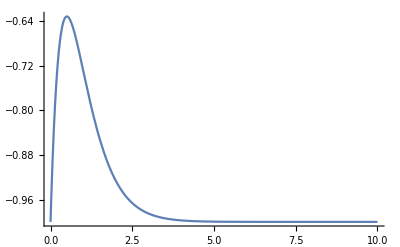

```mathematica
Plot[-1+2 ⅇ^(-2 H1) H1,{H1,0,10},PlotRange->All]
```

0.05

2 (-1+2/ⅇ^2)

-Graphics-

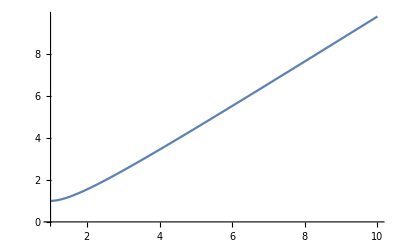

```mathematica
ϵ=0.05
H1=1;
2 (-1+2/ⅇ^2)
Plot[1+(8  (1-2 μ+μ^2))/(μ (Cosh[2]+Sinh[2]))+ϵ 2 H1 (-1+2 ⅇ^(-2 H1) H1) δH μ,{μ,1,10}]
Plot[{1+(8  (1-2 μ+μ^2))/(μ (Cosh[2]+Sinh[2])),ϵ 2 H1 (-1+2 ⅇ^(-2 H1) H1) δH μ},{μ,1,10}]
Clear[ϵ,H1]
```

```mathematica
FullSimplify[Series[U20/(-1/2),{μ,1,2}]//Normal,H1>0]
FullSimplify[Series[U21/(-1/2),{μ,1,1}]//Normal,H1>0]
```

{{1+2 ⅇ^(-2 (H1+δH)) ((-1+ⅇ^(2 δH)) H1^2+2 H1 δH+δH^2) (-1+μ)^2}}

$Aborted

```mathematica
FullSimplify[SeriesCoefficient[U21/(-1/2),{μ,1,1}]//Normal,H1>0]
```

$Aborted

```mathematica
δH=H2-H1
FullSimplify[Expand[ⅇ^(-2 (H1+δH)) (-1-2 H1+ⅇ^(2 δH) (1+2 H1 (1+H1))-2 δH-2 (H1+δH)^2-ⅇ^(2 (H1+δH)) δH (2 H1+δH))]]
Clear[δH]
```

-H1+H2

H1^2+ⅇ^(-2 H1) (1+2 H1 (1+H1))-H2^2+ⅇ^(-2 H2) (-1-2 H2 (1+H2))

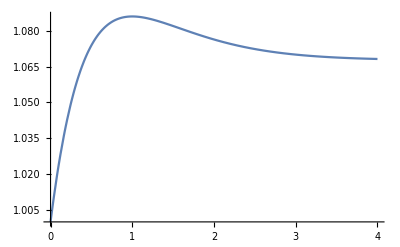

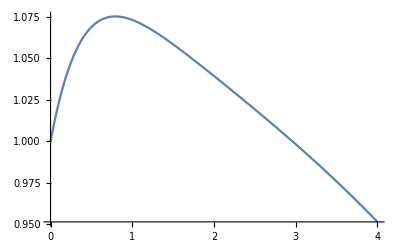

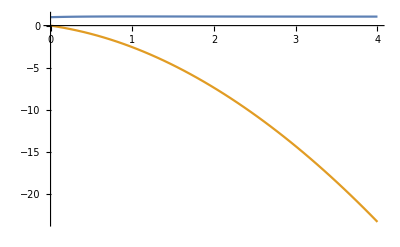

```mathematica
Plot[1+(2 (-1+1.5)^2 (-1+2 δH+δH^2+Cosh[2 δH]+Sinh[2 δH]))/(Cosh[2] Cosh[2 δH]+Cosh[2 δH] Sinh[2]+ⅇ^2 Sinh[2 δH]),{δH,0,4},PlotRange->All]
Plot[1+(2 (-1+1.5)^2 (-1+2 δH+δH^2+Cosh[2 δH]+Sinh[2 δH]))/(Cosh[2] Cosh[2 δH]+Cosh[2 δH] Sinh[2]+ⅇ^2 Sinh[2 δH])+0.005 ⅇ^(-2 (1+δH)) (-5-2 δH (3+δH)+ⅇ^(2 δH) (5-ⅇ^2 δH (2+δH))) ,{δH,0,4},PlotRange->All]
Plot[{1+(2 (-1+1.5)^2 (-1+2 δH+δH^2+Cosh[2 δH]+Sinh[2 δH]))/(Cosh[2] Cosh[2 δH]+Cosh[2 δH] Sinh[2]+ⅇ^2 Sinh[2 δH]), ⅇ^(-2 (1+δH)) (-5-2 δH (3+δH)+ⅇ^(2 δH) (5-ⅇ^2 δH (2+δH)))} ,{δH,0,4},PlotRange->All]
```

```mathematica
Limit[1+2 ⅇ^(-2 (H1+δH)) ((-1+ⅇ^(2 δH)) H1^2+2 H1 δH+δH^2) (-1+μ)^2,δH->∞]
Limit[-ⅇ^(-H1-δH) (Sinh[H1] (-δH ((1+H1) (2+H1 β^2)+δH+(1+H1) β^2 δH) Cosh[δH]+(2-H1^2 (-4+β^2)+H1 (4+β^2+6 δH-3 β^2 δH)+δH (2+β^2+3 δH-2 β^2 δH)) Sinh[δH])+Cosh[H1] (δH (2+H1 (6+(-3+H1) β^2)+3 δH+(-3+H1) β^2 δH) Cosh[δH]-(2-H1^2 (-4+β^2)+δH (2+β^2+δH+2 β^2 δH)+H1 (4+β^2+(2+β^2) δH)) Sinh[δH])),δH->∞]
```

ⅇ^(-2 H1) (ⅇ^(2 H1)+2 H1^2 (-1+μ)^2)

-∞

```mathematica
flow
```

### H1=1. μ=1,

```mathematica
Clear[μ,β,H1,δH]
```

```mathematica
μ=1
```

1

```mathematica
F=(2 √(-1+α^2) μ)/(2 √(-1+α^2) μ Cosh[√(-1+α^2) δH]-2 (H1 (-1+α^2) (β^2-μ) μ+β √((-1+α^2) μ)) Sinh[√(-1+α^2) δH]);
```

```mathematica
Series[F,{ϵ,0,2}]
```

1+√2 β δH √ϵ+(-2 δH+2 β^2 δH-δH^2+2 β^2 δH^2) ϵ+1/12 (3 √2 β δH-48 √2 β δH^2+48 √2 β^3 δH^2-20 √2 β δH^3+24 √2 β^3 δH^3) ϵ^(3/2)+1/6 (-6 δH+6 β^2 δH+21 δH^2-42 β^2 δH^2+24 β^4 δH^2+20 δH^3-92 β^2 δH^3+72 β^4 δH^3+5 δH^4-28 β^2 δH^4+24 β^4 δH^4) ϵ^2+O[ϵ]^(5/2)

```mathematica
U20=FullSimplify[Expand[SeriesCoefficient[1/(-1/2)(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,0}]//Normal]]
U205=FullSimplify[SeriesCoefficient[1/(-1/2)(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,1/2}]//Normal]
U21=FullSimplify[SeriesCoefficient[(1+2 (Evaluate[h110/.lead1]+ϵ Evaluate[h111/.lead3]))F/2,{ϵ,0,1}]//Normal]
```

{{1}}

{{√2 β δH}}

{{1/2 ⅇ^(-H1-δH) (Sinh[H1] (-δH ((1+H1) (2+H1 β^2)+δH+(1+H1) β^2 δH) Cosh[δH]+(2-H1^2 (-4+β^2)+H1 (4+β^2+6 δH-3 β^2 δH)+δH (2+β^2+3 δH-2 β^2 δH)) Sinh[δH])+Cosh[H1] (δH (2+H1 (6+(-3+H1) β^2)+3 δH+(-3+H1) β^2 δH) Cosh[δH]-(2-H1^2 (-4+β^2)+δH (2+β^2+δH+2 β^2 δH)+H1 (4+β^2+(2+β^2) δH)) Sinh[δH]))}}

## Large k

```mathematica
TrigToExp[Cosh[x]]
TrigToExp[Sinh[x]]
```

ⅇ^-x/2+ⅇ^x/2

-ⅇ^-x/2+ⅇ^x/2

```mathematica
Collect[eqns,{Cosh[α δH],Sinh[α δH]},FullSimplify]
```

{-2 (1+α) (F12+2 h12-F12 α^2) μ Cosh[δH]+4 h12 α (1+α) μ Cosh[α δH]-2 (-1+α) (1+α)^2 μ (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+2 F12 β √((-1+α^2) μ) Sinh[δH]+4 h12 β √((-1+α^2) μ) Sinh[δH]+2 F12 α β √((-1+α^2) μ) Sinh[δH]+(2 h12 (-4+(1+α^2) μ (4-(3+α) μ))+F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]+(4 h12 α (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))-2 F12 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))) Sinh[α δH],2 (1+G11 H1) (-1+α) (1+α)^2 μ Cosh[H1]+(-2 h12 (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F12 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]+(4 h12 (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))-2 F12 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))) Cosh[α δH]+2 (1+α) μ (-((G11-H1 h11) (-1+α^2) Sinh[H1])+(-2 h12+F12 (-1+α^2)) Sinh[δH])+4 h12 (1+α) μ Sinh[α δH],4 (1+G11 H1+h11) (-1+α) (1+α)^2 μ Cosh[H1]+2 μ (-2 h12 (4-4 (1+α^2) μ+(3+α) (1+α^2) μ^2+(-1+α) β √((-1+α^2) μ))+F12 (1+α) (-4+4 (1+α^2) μ+(-3+α^2) (1+α^2) μ^2+(1+α^2) β √((-1+α^2) μ))) Cosh[δH]+(4 h12 (2 (1+α^2) μ-4 (1+α^2) μ^2+(3+α) (1+α^2) μ^3+(-1+α) β √((-1+α^2) μ^3))-2 F12 (1+α) (1+α^2) (β √((-1+α^2) μ^3)+μ (-2+μ (4+(-3+α^2) μ)))) Cosh[α δH]+4 H1 h11 (-1+α) (1+α)^2 μ Sinh[H1]-4 F12 β √((-1+α^2) μ) Sinh[δH]-8 h12 β √((-1+α^2) μ) Sinh[δH]-4 F12 α β √((-1+α^2) μ) Sinh[δH]+4 F12 β √((-1+α^2) μ^3) Sinh[δH]+8 h12 β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α^2 β √((-1+α^2) μ^3) Sinh[δH]+8 h12 α^2 β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α^3 β √((-1+α^2) μ^3) Sinh[δH]-3 F12 β √((-1+α^2) μ^5) Sinh[δH]-6 h12 β √((-1+α^2) μ^5) Sinh[δH]-3 F12 α β √((-1+α^2) μ^5) Sinh[δH]-2 h12 α β √((-1+α^2) μ^5) Sinh[δH]-2 F12 α^2 β √((-1+α^2) μ^5) Sinh[δH]-6 h12 α^2 β √((-1+α^2) μ^5) Sinh[δH]-2 F12 α^3 β √((-1+α^2) μ^5) Sinh[δH]-2 h12 α^3 β √((-1+α^2) μ^5) Sinh[δH]+F12 α^4 β √((-1+α^2) μ^5) Sinh[δH]+F12 α^5 β √((-1+α^2) μ^5) Sinh[δH]+2 (1+α) μ (2 h12 (-1+α) β^2-4 h12 μ+F12 (-1+α^2) (β^2+2 μ)) Sinh[δH]+(-2 F12 α (1+α) β ((-1+α^2) β μ-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α^2 √((-1+α^2) μ^5))+4 h12 (-α (-1+α^2) β^2 μ+(1+α) (1+α^2) μ^2+2 α β √((-1+α^2) μ)-4 α β √((-1+α^2) μ^3)+3 α β √((-1+α^2) μ^5)+α^2 β √((-1+α^2) μ^5))) Sinh[α δH],4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]+2 (1+α) (-3+α^2) (-2 h12+F12 (-1+α^2)) μ Cosh[δH]-8 h12 α (1+α) μ Cosh[α δH]+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]-6 F12 β √((-1+α^2) μ) Sinh[δH]-12 h12 β √((-1+α^2) μ) Sinh[δH]-6 F12 α β √((-1+α^2) μ) Sinh[δH]+2 F12 α^2 β √((-1+α^2) μ) Sinh[δH]+4 h12 α^2 β √((-1+α^2) μ) Sinh[δH]+2 F12 α^3 β √((-1+α^2) μ) Sinh[δH]+(-3+α^2) (2 h12 (-4+(1+α^2) μ (4-(3+α) μ))+F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]+4 α (-2 h12 (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))+F12 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))) Sinh[α δH]}

```mathematica
ϵ==ⅇ^(- α δH)
Sinh[α δH]==(-ϵ/2+1/(2ϵ))
Cosh[α δH]==(ϵ/2+1/(2ϵ))
```

```mathematica
h12=ϵ h12s
F12=ϵ F12s
eqnsL=Collect[{-2 (1+α) (F12+2 h12-F12 α^2) μ Cosh[δH]+4 h12 α (1+α) μ (ϵ/2+1/(2ϵ))-2 (-1+α) (1+α)^2 μ (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+2 F12 β √((-1+α^2) μ) Sinh[δH]+4 h12 β √((-1+α^2) μ) Sinh[δH]+2 F12 α β √((-1+α^2) μ) Sinh[δH]+(2 h12 (-4+(1+α^2) μ (4-(3+α) μ))+F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]+(4 h12 α (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))-2 F12 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))) (-ϵ/2+1/(2ϵ)),2 (1+G11 H1) (-1+α) (1+α)^2 μ Cosh[H1]+(-2 h12 (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F12 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]+(4 h12 (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))-2 F12 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ)))(ϵ/2+1/(2ϵ))+2 (1+α) μ (-((G11-H1 h11) (-1+α^2) Sinh[H1])+(-2 h12+F12 (-1+α^2)) Sinh[δH])+4 h12 (1+α) μ (-ϵ/2+1/(2ϵ)),4 (1+G11 H1+h11) (-1+α) (1+α)^2 μ Cosh[H1]+2 μ (-2 h12 (4-4 (1+α^2) μ+(3+α) (1+α^2) μ^2+(-1+α) β √((-1+α^2) μ))+F12 (1+α) (-4+4 (1+α^2) μ+(-3+α^2) (1+α^2) μ^2+(1+α^2) β √((-1+α^2) μ))) Cosh[δH]+(4 h12 (2 (1+α^2) μ-4 (1+α^2) μ^2+(3+α) (1+α^2) μ^3+(-1+α) β √((-1+α^2) μ^3))-2 F12 (1+α) (1+α^2) (β √((-1+α^2) μ^3)+μ (-2+μ (4+(-3+α^2) μ)))) (ϵ/2+1/(2ϵ))+4 H1 h11 (-1+α) (1+α)^2 μ Sinh[H1]-4 F12 β √((-1+α^2) μ) Sinh[δH]-8 h12 β √((-1+α^2) μ) Sinh[δH]-4 F12 α β √((-1+α^2) μ) Sinh[δH]+4 F12 β √((-1+α^2) μ^3) Sinh[δH]+8 h12 β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α^2 β √((-1+α^2) μ^3) Sinh[δH]+8 h12 α^2 β √((-1+α^2) μ^3) Sinh[δH]+4 F12 α^3 β √((-1+α^2) μ^3) Sinh[δH]-3 F12 β √((-1+α^2) μ^5) Sinh[δH]-6 h12 β √((-1+α^2) μ^5) Sinh[δH]-3 F12 α β √((-1+α^2) μ^5) Sinh[δH]-2 h12 α β √((-1+α^2) μ^5) Sinh[δH]-2 F12 α^2 β √((-1+α^2) μ^5) Sinh[δH]-6 h12 α^2 β √((-1+α^2) μ^5) Sinh[δH]-2 F12 α^3 β √((-1+α^2) μ^5) Sinh[δH]-2 h12 α^3 β √((-1+α^2) μ^5) Sinh[δH]+F12 α^4 β √((-1+α^2) μ^5) Sinh[δH]+F12 α^5 β √((-1+α^2) μ^5) Sinh[δH]+2 (1+α) μ (2 h12 (-1+α) β^2-4 h12 μ+F12 (-1+α^2) (β^2+2 μ)) Sinh[δH]+(-2 F12 α (1+α) β ((-1+α^2) β μ-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α^2 √((-1+α^2) μ^5))+4 h12 (-α (-1+α^2) β^2 μ+(1+α) (1+α^2) μ^2+2 α β √((-1+α^2) μ)-4 α β √((-1+α^2) μ^3)+3 α β √((-1+α^2) μ^5)+α^2 β √((-1+α^2) μ^5))) (-ϵ/2+1/(2ϵ)),4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]+2 (1+α) (-3+α^2) (-2 h12+F12 (-1+α^2)) μ Cosh[δH]-8 h12 α (1+α) μ (ϵ/2+1/(2ϵ))+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]-6 F12 β √((-1+α^2) μ) Sinh[δH]-12 h12 β √((-1+α^2) μ) Sinh[δH]-6 F12 α β √((-1+α^2) μ) Sinh[δH]+2 F12 α^2 β √((-1+α^2) μ) Sinh[δH]+4 h12 α^2 β √((-1+α^2) μ) Sinh[δH]+2 F12 α^3 β √((-1+α^2) μ) Sinh[δH]+(-3+α^2) (2 h12 (-4+(1+α^2) μ (4-(3+α) μ))+F12 (1+α) (-4+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]+4 α (-2 h12 (2-β √((-1+α^2) μ)+μ (-4+(3+α) μ))+F12 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))) (-ϵ/2+1/(2ϵ))},ϵ,FullSimplify]
```

h12s ϵ

F12s ϵ

{2 h12s α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F12s α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+α ϵ^2 (2 h12s β √((-1+α^2) μ)-2 h12s (-1+μ) (-2+(3+α) μ)+F12s (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ)))-2 (-1+α) (1+α)^2 μ (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+ϵ (2 (1+α) (-2 h12s+F12s (-1+α^2)) μ Cosh[δH]+(-2 h12s (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F12s (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]),2 h12s (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F12s (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+ϵ^2 (-2 h12s β √((-1+α^2) μ)+2 h12s (-1+μ) (-2+(3+α) μ)-F12s (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ)))+2 (-1+α) (1+α)^2 μ (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1])+ϵ ((-2 h12s (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F12s (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]+2 (1+α) (-2 h12s+F12s (-1+α^2)) μ Sinh[δH]),2 h12s (2 μ+α (β^2+α (2-α β^2)) μ+(-3+α) (1+α^2) μ^2+(3+α) (1+α^2) μ^3-β √((-1+α^2) μ^3)+α β (2 √((-1+α^2) μ)-3 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))-F12s (1+α) (-2 (1+α^2) μ+α (-1+α^2) β^2 μ+4 (1+α^2) μ^2+(-3+α^2) (1+α^2) μ^3+β √((-1+α^2) μ^3)+α β (-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^3)+α √((-1+α^2) μ^5))))+ϵ^2 (2 h12s (2 (1+α^2) μ-4 (1+α^2) μ^2+(3+α) (1+α^2) μ^3+(-1+α) β √((-1+α^2) μ^3))+F12s α (1+α) β ((-1+α^2) β μ-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α^2 √((-1+α^2) μ^5))-2 h12s (-α (-1+α^2) β^2 μ+(1+α) (1+α^2) μ^2+2 α β √((-1+α^2) μ)-4 α β √((-1+α^2) μ^3)+3 α β √((-1+α^2) μ^5)+α^2 β √((-1+α^2) μ^5))-F12s (1+α) (1+α^2) (β √((-1+α^2) μ^3)+μ (-2+μ (4+(-3+α^2) μ))))+4 (-1+α) (1+α)^2 μ ((1+G11 H1+h11) Cosh[H1]+H1 h11 Sinh[H1])+ϵ (2 μ (-2 h12s (4-4 (1+α^2) μ+(3+α) (1+α^2) μ^2+(-1+α) β √((-1+α^2) μ))+F12s (1+α) (-4+4 (1+α^2) μ+(-3+α^2) (1+α^2) μ^2+(1+α^2) β √((-1+α^2) μ))) Cosh[δH]+(F12s (1+α) (2 (-1+α^2) β^2 μ+4 (-1+α^2) μ^2+β (-4 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α^2 (4 √((-1+α^2) μ^3)-2 √((-1+α^2) μ^5)+α^2 √((-1+α^2) μ^5))))-2 h12s (-2 (-1+α^2) β^2 μ+4 (1+α) μ^2+β (4 √((-1+α^2) μ)-4 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^5)+α (-4 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))))) Sinh[δH]),4 h12s α (-2+β √((-1+α^2) μ)-μ (-3+α+(3+α) μ))+2 F12s α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+ϵ^2 (4 h12s α (-β √((-1+α^2) μ)+(-1+μ) (-2+(3+α) μ))-2 F12s α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ)))+4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]+(-3+α^2) ϵ (2 (1+α) (-2 h12s+F12s (-1+α^2)) μ Cosh[δH]+(-2 h12s (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F12s (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH])}

```mathematica
F12s =F120+ϵ F121 +ϵ^2 F122
G11 =G110+ϵ G111 +ϵ^2 G112
h11 =h110+ϵ h111 +ϵ^2 h112
h12s=h120+ϵ h121 +ϵ^2 h122
Series[eqnsL,{ϵ,0,0}]//Normal
```

F120+F121 ϵ+F122 ϵ^2

G110+G111 ϵ+G112 ϵ^2

h110+h111 ϵ+h112 ϵ^2

h120+h121 ϵ+h122 ϵ^2

{2 h120 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F120 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))-2 (-1+α) (1+α)^2 μ (H1 h110 Cosh[H1]+(1+G110 H1+h110) Sinh[H1]),2 h120 (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F120 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+2 (-1+α) (1+α)^2 μ (Cosh[H1]+G110 H1 Cosh[H1]-G110 Sinh[H1]+H1 h110 Sinh[H1]),2 h120 (2 μ+α (β^2+α (2-α β^2)) μ+(-3+α) (1+α^2) μ^2+(3+α) (1+α^2) μ^3-β √((-1+α^2) μ^3)+α β (2 √((-1+α^2) μ)-3 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))-F120 (1+α) (-2 (1+α^2) μ+α (-1+α^2) β^2 μ+4 (1+α^2) μ^2+(-3+α^2) (1+α^2) μ^3+β √((-1+α^2) μ^3)+α β (-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^3)+α √((-1+α^2) μ^5))))+4 (-1+α) (1+α)^2 μ ((1+G110 H1+h110) Cosh[H1]+H1 h110 Sinh[H1]),4 h120 α (-2+β √((-1+α^2) μ)-μ (-3+α+(3+α) μ))+2 F120 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+4 (G110+H1 h110) (-1+α) (1+α)^2 Cosh[H1]+4 (1+G110 H1+2 h110) (-1+α) (1+α)^2 Sinh[H1]}

```mathematica
l1=Solve[{2 h120 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F120 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))-2 (-1+α) (1+α)^2 μ (H1 h110 Cosh[H1]+(1+G110 H1+h110) Sinh[H1])==0,2 h120 (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F120 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+2 (-1+α) (1+α)^2 μ (Cosh[H1]+G110 H1 Cosh[H1]-G110 Sinh[H1]+H1 h110 Sinh[H1])==0,2 h120 (2 μ+α (β^2+α (2-α β^2)) μ+(-3+α) (1+α^2) μ^2+(3+α) (1+α^2) μ^3-β √((-1+α^2) μ^3)+α β (2 √((-1+α^2) μ)-3 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))-F120 (1+α) (-2 (1+α^2) μ+α (-1+α^2) β^2 μ+4 (1+α^2) μ^2+(-3+α^2) (1+α^2) μ^3+β √((-1+α^2) μ^3)+α β (-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^3)+α √((-1+α^2) μ^5))))+4 (-1+α) (1+α)^2 μ ((1+G110 H1+h110) Cosh[H1]+H1 h110 Sinh[H1])==0,-4 h120 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))+2 F120 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+4 (G110+H1 h110) (-1+α) (1+α)^2 Cosh[H1]+4 (1+G110 H1+2 h110) (-1+α) (1+α)^2 Sinh[H1]==0},{h110,G110,h120,F120}];
```

```mathematica
SeriesCoefficient[eqnsL,{ϵ,0,1}]
```

{2 h121 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F121 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+2 (1+α) (-2 h120+F120 (-1+α^2)) μ Cosh[δH]-2 (-1+α) (1+α)^2 μ (H1 h111 Cosh[H1]+(G111 H1+h111) Sinh[H1])+(2 h120 (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4-(3+α) μ))+F120 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH],2 h121 (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F121 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+(2 h120 (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4-(3+α) μ))+F120 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]+2 (-1+α) (1+α)^2 μ (G111 H1 Cosh[H1]-G111 Sinh[H1]+H1 h111 Sinh[H1])+2 (1+α) (-2 h120+F120 (-1+α^2)) μ Sinh[δH],2 h121 (2 μ+α (β^2+α (2-α β^2)) μ+(-3+α) (1+α^2) μ^2+(3+α) (1+α^2) μ^3-β √((-1+α^2) μ^3)+α β (2 √((-1+α^2) μ)-3 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))-F121 (1+α) (-2 (1+α^2) μ+α (-1+α^2) β^2 μ+4 (1+α^2) μ^2+(-3+α^2) (1+α^2) μ^3+β √((-1+α^2) μ^3)+α β (-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^3)+α √((-1+α^2) μ^5))))+2 μ (-2 h120 (4-4 (1+α^2) μ+(3+α) (1+α^2) μ^2+(-1+α) β √((-1+α^2) μ))+F120 (1+α) (-4+4 (1+α^2) μ+(-3+α^2) (1+α^2) μ^2+(1+α^2) β √((-1+α^2) μ))) Cosh[δH]+4 (-1+α) (1+α)^2 μ ((G111 H1+h111) Cosh[H1]+H1 h111 Sinh[H1])+(F120 (1+α) (2 (-1+α^2) β^2 μ+4 (-1+α^2) μ^2+β (-4 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α^2 (4 √((-1+α^2) μ^3)-2 √((-1+α^2) μ^5)+α^2 √((-1+α^2) μ^5))))-2 h120 (-2 (-1+α^2) β^2 μ+4 (1+α) μ^2+β (4 √((-1+α^2) μ)-4 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^5)+α (-4 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))))) Sinh[δH],-4 h121 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))+2 F121 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+4 (G111+H1 h111) (-1+α) (1+α)^2 Cosh[H1]+4 (G111 H1+2 h111) (-1+α) (1+α)^2 Sinh[H1]+(-3+α^2) (2 (1+α) (-2 h120+F120 (-1+α^2)) μ Cosh[δH]+(-2 h120 (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F120 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH])}

```mathematica
l2=Solve[{2 h121 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F121 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+2 (1+α) (-2 h120+F120 (-1+α^2)) μ Cosh[δH]-2 (-1+α) (1+α)^2 μ (H1 h111 Cosh[H1]+(G111 H1+h111) Sinh[H1])+(2 h120 (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4-(3+α) μ))+F120 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH]==0,2 h121 (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))-F121 (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+(2 h120 (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4-(3+α) μ))+F120 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Cosh[δH]+2 (-1+α) (1+α)^2 μ (G111 H1 Cosh[H1]-G111 Sinh[H1]+H1 h111 Sinh[H1])+2 (1+α) (-2 h120+F120 (-1+α^2)) μ Sinh[δH]==0,2 h121 (2 μ+α (β^2+α (2-α β^2)) μ+(-3+α) (1+α^2) μ^2+(3+α) (1+α^2) μ^3-β √((-1+α^2) μ^3)+α β (2 √((-1+α^2) μ)-3 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))-F121 (1+α) (-2 (1+α^2) μ+α (-1+α^2) β^2 μ+4 (1+α^2) μ^2+(-3+α^2) (1+α^2) μ^3+β √((-1+α^2) μ^3)+α β (-2 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^3)+α √((-1+α^2) μ^5))))+2 μ (-2 h120 (4-4 (1+α^2) μ+(3+α) (1+α^2) μ^2+(-1+α) β √((-1+α^2) μ))+F120 (1+α) (-4+4 (1+α^2) μ+(-3+α^2) (1+α^2) μ^2+(1+α^2) β √((-1+α^2) μ))) Cosh[δH]+4 (-1+α) (1+α)^2 μ ((G111 H1+h111) Cosh[H1]+H1 h111 Sinh[H1])+(F120 (1+α) (2 (-1+α^2) β^2 μ+4 (-1+α^2) μ^2+β (-4 √((-1+α^2) μ)+4 √((-1+α^2) μ^3)-3 √((-1+α^2) μ^5)+α^2 (4 √((-1+α^2) μ^3)-2 √((-1+α^2) μ^5)+α^2 √((-1+α^2) μ^5))))-2 h120 (-2 (-1+α^2) β^2 μ+4 (1+α) μ^2+β (4 √((-1+α^2) μ)-4 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α (√((-1+α^2) μ^5)+α (-4 √((-1+α^2) μ^3)+3 √((-1+α^2) μ^5)+α √((-1+α^2) μ^5)))))) Sinh[δH]==0,-4 h121 α (2-β √((-1+α^2) μ)+μ (-3+α+(3+α) μ))+2 F121 α (1+α) (-2+β √((-1+α^2) μ)+μ (4+(-3+α^2) μ))+4 (G111+H1 h111) (-1+α) (1+α)^2 Cosh[H1]+4 (G111 H1+2 h111) (-1+α) (1+α)^2 Sinh[H1]+(-3+α^2) (2 (1+α) (-2 h120+F120 (-1+α^2)) μ Cosh[δH]+(-2 h120 (4-2 β √((-1+α^2) μ)+(1+α^2) μ (-4+(3+α) μ))+F120 (1+α) (-4+2 β √((-1+α^2) μ)+(1+α^2) μ (4+(-3+α^2) μ))) Sinh[δH])==0},{h111,G111,h121,F121}];
l3=Evaluate[l2/.l1];
```

### μ=1,β=0

```mathematica
Clear[μ,β]
```

```mathematica
μ=1
β=0
```

1

0

```mathematica
Collect[eqns,{Cosh[α δH],Sinh[α δH]},FullSimplify]
```

{4 h12 α (1+α) Cosh[α δH]+(1+α) (-2 (F12+2 h12-F12 α^2) Cosh[δH]-2 (-1+α^2) (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Sinh[δH])-2 α (1+α) (-2 h12+F12 (-1+α^2)) Sinh[α δH],2 (1+α) (F12+2 h12-F12 α^2) Cosh[α δH]+(1+α) ((-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+2 (-1+α^2) (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1])-2 (F12+2 h12-F12 α^2) Sinh[δH])+4 h12 (1+α) Sinh[α δH],-2 (1+α) (1+α^2) (-2 h12+F12 (-1+α^2)) Cosh[α δH]+2 (1+α) ((-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+2 (-1+α^2) ((1+G11 H1+h11) Cosh[H1]+H1 h11 Sinh[H1])-2 (F12+2 h12-F12 α^2) Sinh[δH])+4 h12 (1+α) (1+α^2) Sinh[α δH],-8 h12 α (1+α) Cosh[α δH]+(1+α) (4 (G11+H1 h11) (-1+α^2) Cosh[H1]+4 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1]+(-3+α^2) (-2 (F12+2 h12-F12 α^2) Cosh[δH]+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Sinh[δH]))+4 α (1+α) (-2 h12+F12 (-1+α^2)) Sinh[α δH]}

```mathematica
h12=ϵ h12s
F12=ϵ F12s
eqnsL=Collect[{4 h12 α (1+α) (ϵ/2+1/(2ϵ))+(1+α) (-2 (F12+2 h12-F12 α^2) Cosh[δH]-2 (-1+α^2) (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Sinh[δH])-2 α (1+α) (-2 h12+F12 (-1+α^2))(-ϵ/2+1/(2ϵ)),2 (1+α) (F12+2 h12-F12 α^2) (ϵ/2+1/(2ϵ))+(1+α) ((-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+2 (-1+α^2) (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1])-2 (F12+2 h12-F12 α^2) Sinh[δH])+4 h12 (1+α) (-ϵ/2+1/(2ϵ)),-2 (1+α) (1+α^2) (-2 h12+F12 (-1+α^2))(ϵ/2+1/(2ϵ))+2 (1+α) ((-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+2 (-1+α^2) ((1+G11 H1+h11) Cosh[H1]+H1 h11 Sinh[H1])-2 (F12+2 h12-F12 α^2) Sinh[δH])+4 h12 (1+α) (1+α^2) (-ϵ/2+1/(2ϵ)),-8 h12 α (1+α) (ϵ/2+1/(2ϵ))+(1+α) (4 (G11+H1 h11) (-1+α^2) Cosh[H1]+4 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1]+(-3+α^2) (-2 (F12+2 h12-F12 α^2) Cosh[δH]+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Sinh[δH]))+4 α (1+α) (-2 h12+F12 (-1+α^2)) (-ϵ/2+1/(2ϵ))},ϵ,FullSimplify]
```

h12s ϵ

F12s ϵ

{F12s α (1+α) (-1+α^2) ϵ^2+(1+α) (4 h12s α-F12s α (-1+α^2)-2 (-1+α^2) (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1]))+(1+α) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH]),-F12s (1+α) (-1+α^2) ϵ^2+(1+α) (F12s+4 h12s-F12s α^2+2 (-1+α^2) (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1]))+(1+α) ϵ ((-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Cosh[δH]-2 (F12s+2 h12s-F12s α^2) Sinh[δH]),-F12s (-1-α+α^4+α^5) ϵ^2+(1+α) (F12s-F12s α^4+4 h12s (1+α^2)+4 (-1+α^2) ((1+G11 H1+h11) Cosh[H1]+H1 h11 Sinh[H1]))+2 (1+α) ϵ ((-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Cosh[δH]-2 (F12s+2 h12s-F12s α^2) Sinh[δH]),-2 F12s α (1+α) (-1+α^2) ϵ^2+2 (1+α) (-((F12s+4 h12s) α)+F12s α^3+2 (G11+H1 h11) (-1+α^2) Cosh[H1]+2 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1])+(1+α) (-3+α^2) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH])}

```mathematica
Clear[F12s,G11,h11,h12s]
```

```mathematica
ans2=Solve[{F12s α (1+α) (-1+α^2) ϵ^2+(1+α) (4 h12s α-F12s α (-1+α^2)-2 (-1+α^2) (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1]))+(1+α) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH])==0,-F12s (1+α) (-1+α^2) ϵ^2+(1+α) (F12s+4 h12s-F12s α^2+2 (-1+α^2) (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1]))+(1+α) ϵ ((-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Cosh[δH]-2 (F12s+2 h12s-F12s α^2) Sinh[δH])==0,-F12s (-1-α+α^4+α^5) ϵ^2+(1+α) (F12s-F12s α^4+4 h12s (1+α^2)+4 (-1+α^2) ((1+G11 H1+h11) Cosh[H1]+H1 h11 Sinh[H1]))+2 (1+α) ϵ ((-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Cosh[δH]-2 (F12s+2 h12s-F12s α^2) Sinh[δH])==0,-2 F12s α (1+α) (-1+α^2) ϵ^2+2 (1+α) (-((F12s+4 h12s) α)+F12s α^3+2 (G11+H1 h11) (-1+α^2) Cosh[H1]+2 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1])+(1+α) (-3+α^2) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH])==0},{F12s,G11,h11,h12s}]
```

```mathematica
η==(ⅇ^(-√(α^2-1)δH))/ⅇ^(-α δH)
Cosh[√(-1+α^2) δH]==((ϵ η)/2+1/(2ϵ η))
Sinh[√(-1+α^2) δH]==(-(ϵ η)/2+1/(2ϵ η))
```

```mathematica
F=FullSimplify[(2 √(-1+α^2) μ)/(2 √(-1+α^2) μ ((ϵ η)/2+1/(2ϵ η))-2 (H1 (-1+α^2) (β^2-μ) μ+β √((-1+α^2) μ)) (-(ϵ η)/2+1/(2ϵ η)))]
```

(2 √(-1+α^2) ϵ η)/(-H1 (-1+α^2) (-1+ϵ^2 η^2)+√(-1+α^2) (1+ϵ^2 η^2))

```mathematica
U2=(1+2 (Evaluate[h11/.ans2]))F/2;
```

```mathematica
FullSimplify[Series[U2,{ϵ,0,1}]//Normal,α>1&& δH>0 && H1>0]
```

{(√(-1+α^2) ϵ η (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/((√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))}

```mathematica
α=√(k+1)
```

√(1+k)

```mathematica
FullSimplify[{(√(-1+α^2) ϵ η (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/((√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))}]
```

{(ϵ η (2 Cosh[δH] (-16 √(1+k)+k (-4-k-4 √(1+k)+ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))+4 k √(1+k) Sinh[2 H1])+(32+(-1+2 H1^2) k^3+8 k (3+√(1+k)+2 H1 √(1+k))+k^2 (-2 √(1+k)+4 H1 (1+H1) (2+√(1+k)))+k (4+k) (4+k+2 √(1+k)) Cosh[2 H1]+2 k (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))/((1+H1 √k) (2 Cosh[δH] (-16 √(1+k)+k (-4+k-4 √(1+k)-ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))-4 k √(1+k) Sinh[2 H1])+32 Sinh[δH]+k ((1+2 H1^2) k^2+8 (3+√(1+k)+2 H1 √(1+k))+2 k (4+√(1+k)+2 H1 (1+H1) (2+√(1+k)))-(4+k) (4+k+2 √(1+k)) Cosh[2 H1]-2 (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))}

```mathematica
FullSimplify[Series[{(ϵ η (2 Cosh[δH] (-16 √(1+k)+k (-4-k-4 √(1+k)+ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))+4 k √(1+k) Sinh[2 H1])+(32+(-1+2 H1^2) k^3+8 k (3+√(1+k)+2 H1 √(1+k))+k^2 (-2 √(1+k)+4 H1 (1+H1) (2+√(1+k)))+k (4+k) (4+k+2 √(1+k)) Cosh[2 H1]+2 k (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))/((1+H1 √k) (2 Cosh[δH] (-16 √(1+k)+k (-4+k-4 √(1+k)-ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))-4 k √(1+k) Sinh[2 H1])+32 Sinh[δH]+k ((1+2 H1^2) k^2+8 (3+√(1+k)+2 H1 √(1+k))+2 k (4+√(1+k)+2 H1 (1+H1) (2+√(1+k)))-(4+k) (4+k+2 √(1+k)) Cosh[2 H1]-2 (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))}/(-1/2),{k,∞,1}],k>0]
```

{((2 ϵ η)/H1+(8 H1 ϵ η)/(-1-2 H1^2+Cosh[2 H1])) √(1/k)-(ϵ η (3+16 H1^2-8 H1^4-4 (1+4 H1^2) Cosh[2 H1]+Cosh[4 H1]+16 H1^3 Sinh[2 H1]))/((H1+2 H1^3-H1 Cosh[2 H1])^2 k)+O[1/k]^(3/2)}

```mathematica
FullSimplify[(ϵ η (1+8 H1^2-4 H1^4+Cosh[2 H1] (-2-8 H1^2+Cosh[2 H1])+8 H1^3 Sinh[2 H1]))/(H1^2 (-1-2 H1^2+Cosh[2 H1])^2 k),H1>0]
```

(ϵ η (1+8 H1^2-4 H1^4+Cosh[2 H1] (-2-8 H1^2+Cosh[2 H1])+8 H1^3 Sinh[2 H1]))/(H1^2 k (-1-2 H1^2+Cosh[2 H1])^2)

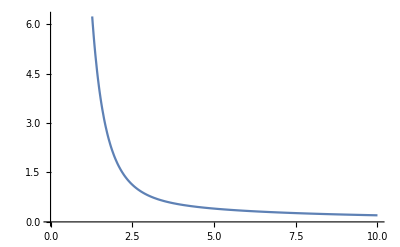

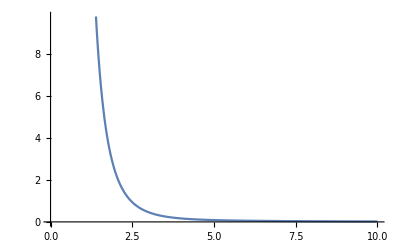

```mathematica
Plot[2/H1+(8 H1)/(-1-2 H1^2+Cosh[2 H1]),{H1,0,10}]
Plot[(3+16 H1^2-8 H1^4-4 (1+4 H1^2) Cosh[2 H1]+Cosh[4 H1]+16 H1^3 Sinh[2 H1])/((H1+2 H1^3-H1 Cosh[2 H1])^2),{H1,0,10}]
```

```mathematica
ux1==FullSimplify[Series[-U2 ((ϵ η)/2+1/(2ϵ η))+(U2 (H1 (-1+α^2) (β^2-μ) μ+2 β √((-1+α^2) μ)) (-(ϵ η)/2+1/(2ϵ η)))/(2 √(-1+α^2) μ),{ϵ,0,0}]//Normal]
```

ux1=={-(((2 √(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/(4 (√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])))}

```mathematica
Limit[-(((2 √(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/(4 (√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))),α->∞]
```

(-1+2 H1^2+Cosh[2 H1])/(4 (-1-2 H1^2+Cosh[2 H1]))

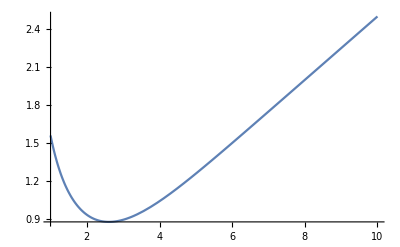

```mathematica
Plot[(-1+2 H1^2+Cosh[2 H1])/(4 (-1-2 H1^2+Cosh[2 H1]))H1,{H1,1,10},PlotRange->All]
```

```mathematica
ux2==FullSimplify[Series[-(U2 (β-β ((ϵ η)/2+1/(2ϵ η))+√μ (-(ϵ η)/2+1/(2ϵ η))))/(√(-1+α^2) δH √μ),{ϵ,0,0}]//Normal]
```

ux2=={(2 Cosh[δH] (-2 H1^2 (-1+α^2)^2+2 H1 (-3+2 α^2+α^4)+(3+α^2) (-1+α (4+α))-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])-(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])/(2 (√(-1+α^2)+H1 (-1+α^2)) δH (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))}

```mathematica
Limit[(2 Cosh[δH] (-2 H1^2 (-1+α^2)^2+2 H1 (-3+2 α^2+α^4)+(3+α^2) (-1+α (4+α))-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])-(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])/(2 (√(-1+α^2)+H1 (-1+α^2)) δH (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])),α->∞]
```

0

### H1=1. β=0,

```mathematica
Clear[μ,β,H1,δH]
```

```mathematica
H1=1
β=0
```

1

0

### μ=1,

```mathematica
Clear[μ,β]
```

```mathematica
μ=1
```

1

```mathematica
Collect[eqns,{Cosh[α δH],Sinh[α δH]},FullSimplify]
```

{-2 (1+α) (F12s+2 h12s-F12s α^2) ϵ Cosh[δH]+4 h12s α (1+α) ϵ Cosh[α δH]-2 (-1+α) (1+α)^2 (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+(1+α) (-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) ϵ Sinh[δH]+2 F12s √(-1+α^2) β ϵ Sinh[δH]+4 h12s √(-1+α^2) β ϵ Sinh[δH]+2 F12s α √(-1+α^2) β ϵ Sinh[δH]+2 α (2 h12s (1+α-√(-1+α^2) β)-F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ Sinh[α δH],2 (1+G11 H1) (-1+α) (1+α)^2 Cosh[H1]+(-2 h12s (3+α-α^2+α^3-2 √(-1+α^2) β)+F12s (1+α) (-3+2 α^2+α^4+2 √(-1+α^2) β)) ϵ Cosh[δH]+(4 h12s (1+α-√(-1+α^2) β) ϵ-2 F12s (1+α) (-1+α^2+√(-1+α^2) β) ϵ) Cosh[α δH]+2 (1+α) (-((G11-H1 h11) (-1+α^2) Sinh[H1])+(-2 h12s+F12s (-1+α^2)) ϵ Sinh[δH])+4 h12s (1+α) ϵ Sinh[α δH],4 (1+G11 H1+h11) (-1+α) (1+α)^2 Cosh[H1]+2 (-2 h12s (3-√(-1+α^2) β+α (1+(-1+α) α+√(-1+α^2) β))+F12s (1+α) (-3+√(-1+α^2) β+α^2 (2+α^2+√(-1+α^2) β))) ϵ Cosh[δH]+(-2 F12s (1+α) (1+α^2) (-1+α^2+√(-1+α^2) β) ϵ+4 h12s (1+α+α^2+α^3-√(-1+α^2) β+α √(-1+α^2) β) ϵ) Cosh[α δH]+(1+α) (4 H1 h11 (-1+α^2) Sinh[H1]+(F12s (-1+α^2) (4+√(-1+α^2) (3+α^2) β+2 β^2)-2 h12s (4+(3+(-2+α) α) √(-1+α^2) β-2 (-1+α) β^2)) ϵ Sinh[δH])-2 (1+α) (F12s α (-1+α^2) β (√(-1+α^2)+β)-2 (h12s+h12s α (α-α β^2+β (√(-1+α^2)+β)))) ϵ Sinh[α δH],4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]-8 h12s α (1+α) ϵ Cosh[α δH]+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]-6 F12s √(-1+α^2) β ϵ Sinh[δH]-12 h12s √(-1+α^2) β ϵ Sinh[δH]-6 F12s α √(-1+α^2) β ϵ Sinh[δH]+2 F12s α^2 √(-1+α^2) β ϵ Sinh[δH]+4 h12s α^2 √(-1+α^2) β ϵ Sinh[δH]+2 F12s α^3 √(-1+α^2) β ϵ Sinh[δH]+(1+α) (-3+α^2) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH])+4 α (-2 h12s (1+α-√(-1+α^2) β)+F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ Sinh[α δH]}

```mathematica
{4 h12 α (1+α) +(1+α) (-2 (F12+2 h12-F12 α^2) Cosh[δH]-2 (-1+α^2) (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Sinh[δH])-2 α (1+α) (-2 h12+F12 (-1+α^2))(-ϵ/2+1/(2ϵ)),2 (1+α) (F12+2 h12-F12 α^2) (ϵ/2+1/(2ϵ))+(1+α) ((-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+2 (-1+α^2) (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1])-2 (F12+2 h12-F12 α^2) Sinh[δH])+4 h12 (1+α) (-ϵ/2+1/(2ϵ)),-2 (1+α) (1+α^2) (-2 h12+F12 (-1+α^2))(ϵ/2+1/(2ϵ))+2 (1+α) ((-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Cosh[δH]+2 (-1+α^2) ((1+G11 H1+h11) Cosh[H1]+H1 h11 Sinh[H1])-2 (F12+2 h12-F12 α^2) Sinh[δH])+4 h12 (1+α) (1+α^2) (-ϵ/2+1/(2ϵ)),-8 h12 α (1+α) (ϵ/2+1/(2ϵ))+(1+α) (4 (G11+H1 h11) (-1+α^2) Cosh[H1]+4 (1+G11 H1+2 h11) (-1+α^2) Sinh[H1]+(-3+α^2) (-2 (F12+2 h12-F12 α^2) Cosh[δH]+(-2 h12 (3+(-2+α) α)+F12 (-3+2 α^2+α^4)) Sinh[δH]))+4 α (1+α) (-2 h12+F12 (-1+α^2)) (-ϵ/2+1/(2ϵ))}
```

```mathematica
h12=ϵ h12s
F12=ϵ F12s
eqnsL=Collect[{-2 (1+α) (F12s+2 h12s-F12s α^2) ϵ Cosh[δH]+4 h12s α (1+α) ϵ (ϵ/2+1/(2ϵ))-2 (-1+α) (1+α)^2 (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+(1+α) (-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) ϵ Sinh[δH]+2 F12s √(-1+α^2) β ϵ Sinh[δH]+4 h12s √(-1+α^2) β ϵ Sinh[δH]+2 F12s α √(-1+α^2) β ϵ Sinh[δH]+2 α (2 h12s (1+α-√(-1+α^2) β)-F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ (-ϵ/2+1/(2ϵ))==0,2 (1+G11 H1) (-1+α) (1+α)^2 Cosh[H1]+(-2 h12s (3+α-α^2+α^3-2 √(-1+α^2) β)+F12s (1+α) (-3+2 α^2+α^4+2 √(-1+α^2) β)) ϵ Cosh[δH]+(4 h12s (1+α-√(-1+α^2) β) ϵ-2 F12s (1+α) (-1+α^2+√(-1+α^2) β) ϵ) (ϵ/2+1/(2ϵ))+2 (1+α) (-((G11-H1 h11) (-1+α^2) Sinh[H1])+(-2 h12s+F12s (-1+α^2)) ϵ Sinh[δH])+4 h12s (1+α) ϵ (-ϵ/2+1/(2ϵ))==0,4 (1+G11 H1+h11) (-1+α) (1+α)^2 Cosh[H1]+2 (-2 h12s (3-√(-1+α^2) β+α (1+(-1+α) α+√(-1+α^2) β))+F12s (1+α) (-3+√(-1+α^2) β+α^2 (2+α^2+√(-1+α^2) β))) ϵ Cosh[δH]+(-2 F12s (1+α) (1+α^2) (-1+α^2+√(-1+α^2) β) ϵ+4 h12s (1+α+α^2+α^3-√(-1+α^2) β+α √(-1+α^2) β) ϵ) (ϵ/2+1/(2ϵ))+(1+α) (4 H1 h11 (-1+α^2) Sinh[H1]+(F12s (-1+α^2) (4+√(-1+α^2) (3+α^2) β+2 β^2)-2 h12s (4+(3+(-2+α) α) √(-1+α^2) β-2 (-1+α) β^2)) ϵ Sinh[δH])-2 (1+α) (F12s α (-1+α^2) β (√(-1+α^2)+β)-2 (h12s+h12s α (α-α β^2+β (√(-1+α^2)+β)))) ϵ (-ϵ/2+1/(2ϵ))==0,4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]-8 h12s α (1+α) ϵ (ϵ/2+1/(2ϵ))+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]-6 F12s √(-1+α^2) β ϵ Sinh[δH]-12 h12s √(-1+α^2) β ϵ Sinh[δH]-6 F12s α √(-1+α^2) β ϵ Sinh[δH]+2 F12s α^2 √(-1+α^2) β ϵ Sinh[δH]+4 h12s α^2 √(-1+α^2) β ϵ Sinh[δH]+2 F12s α^3 √(-1+α^2) β ϵ Sinh[δH]+(1+α) (-3+α^2) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH])+4 α (-2 h12s (1+α-√(-1+α^2) β)+F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ (-ϵ/2+1/(2ϵ))==0},ϵ,FullSimplify]
```

h12s ϵ

F12s ϵ

{2 h12s α (1+α)+α (2 h12s (1+α-√(-1+α^2) β)-F12s (1+α) (-1+α^2+√(-1+α^2) β))+α (2 h12s √(-1+α^2) β+F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ^2-2 (-1+α) (1+α)^2 (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+ϵ (2 (1+α) (-2 h12s+F12s (-1+α^2)) Cosh[δH]+(-2 h12s (3+α-α^2+α^3-2 √(-1+α^2) β)+F12s (1+α) (-3+2 α^2+α^4+2 √(-1+α^2) β)) Sinh[δH])==0,2 h12s (2+2 α-√(-1+α^2) β)-F12s (1+α) (-1+α^2+√(-1+α^2) β)+(-2 h12s √(-1+α^2) β-F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ^2+2 (-1+α) (1+α)^2 (Cosh[H1]+G11 H1 Cosh[H1]-G11 Sinh[H1]+H1 h11 Sinh[H1])+ϵ ((-2 h12s (3+α-α^2+α^3-2 √(-1+α^2) β)+F12s (1+α) (-3+2 α^2+α^4+2 √(-1+α^2) β)) Cosh[δH]+2 (1+α) (-2 h12s+F12s (-1+α^2)) Sinh[δH])==0,-F12s (1+α) (1+α^2) (-1+α^2+√(-1+α^2) β)+2 h12s (1+α+α^2+α^3-√(-1+α^2) β+α √(-1+α^2) β)-(1+α) (F12s α (-1+α^2) β (√(-1+α^2)+β)-2 (h12s+h12s α (α-α β^2+β (√(-1+α^2)+β))))+(-F12s (1+α) (-1+α^4+√(-1+α^2) β+α^2 √(-1+α^2) β+α β (√(-1+α^2)+β)-α^3 β (√(-1+α^2)+β))-2 h12s β (√(-1+α^2)+α (β+α (√(-1+α^2)-α β)))) ϵ^2+4 (1+G11 H1+h11) (-1+α) (1+α)^2 Cosh[H1]+4 H1 h11 (-1+α) (1+α)^2 Sinh[H1]+ϵ (2 (-2 h12s (3-√(-1+α^2) β+α (1+(-1+α) α+√(-1+α^2) β))+F12s (1+α) (-3+√(-1+α^2) β+α^2 (2+α^2+√(-1+α^2) β))) Cosh[δH]+(1+α) (F12s (-1+α^2) (4+√(-1+α^2) (3+α^2) β+2 β^2)-2 h12s (4+(3+(-2+α) α) √(-1+α^2) β-2 (-1+α) β^2)) Sinh[δH])==0,4 h12s α (-2-2 α+√(-1+α^2) β)+2 F12s α (1+α) (-1+α^2+√(-1+α^2) β)+(-4 h12s α √(-1+α^2) β-2 F12s α (1+α) (-1+α^2+√(-1+α^2) β)) ϵ^2+4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]+(-3+α^2) ϵ (2 (1+α) (-2 h12s+F12s (-1+α^2)) Cosh[δH]+(-2 h12s (3+α-α^2+α^3-2 √(-1+α^2) β)+F12s (1+α) (-3+2 α^2+α^4+2 √(-1+α^2) β)) Sinh[δH])==0}

```mathematica
Clear[F12s,G11,h11,h12s]
```

```mathematica
ans2=Solve[{-2 (1+α) (F12s+2 h12s-F12s α^2) ϵ Cosh[δH]+4 h12s α (1+α) ϵ (ϵ/2+1/(2ϵ))-2 (-1+α) (1+α)^2 (H1 h11 Cosh[H1]+(1+G11 H1+h11) Sinh[H1])+(1+α) (-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) ϵ Sinh[δH]+2 F12s √(-1+α^2) β ϵ Sinh[δH]+4 h12s √(-1+α^2) β ϵ Sinh[δH]+2 F12s α √(-1+α^2) β ϵ Sinh[δH]+2 α (2 h12s (1+α-√(-1+α^2) β)-F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ (-ϵ/2+1/(2ϵ))==0,2 (1+G11 H1) (-1+α) (1+α)^2 Cosh[H1]+(-2 h12s (3+α-α^2+α^3-2 √(-1+α^2) β)+F12s (1+α) (-3+2 α^2+α^4+2 √(-1+α^2) β)) ϵ Cosh[δH]+(4 h12s (1+α-√(-1+α^2) β) ϵ-2 F12s (1+α) (-1+α^2+√(-1+α^2) β) ϵ) (ϵ/2+1/(2ϵ))+2 (1+α) (-((G11-H1 h11) (-1+α^2) Sinh[H1])+(-2 h12s+F12s (-1+α^2)) ϵ Sinh[δH])+4 h12s (1+α) ϵ (-ϵ/2+1/(2ϵ))==0,4 (1+G11 H1+h11) (-1+α) (1+α)^2 Cosh[H1]+2 (-2 h12s (3-√(-1+α^2) β+α (1+(-1+α) α+√(-1+α^2) β))+F12s (1+α) (-3+√(-1+α^2) β+α^2 (2+α^2+√(-1+α^2) β))) ϵ Cosh[δH]+(-2 F12s (1+α) (1+α^2) (-1+α^2+√(-1+α^2) β) ϵ+4 h12s (1+α+α^2+α^3-√(-1+α^2) β+α √(-1+α^2) β) ϵ) (ϵ/2+1/(2ϵ))+(1+α) (4 H1 h11 (-1+α^2) Sinh[H1]+(F12s (-1+α^2) (4+√(-1+α^2) (3+α^2) β+2 β^2)-2 h12s (4+(3+(-2+α) α) √(-1+α^2) β-2 (-1+α) β^2)) ϵ Sinh[δH])-2 (1+α) (F12s α (-1+α^2) β (√(-1+α^2)+β)-2 (h12s+h12s α (α-α β^2+β (√(-1+α^2)+β)))) ϵ (-ϵ/2+1/(2ϵ))==0,4 (G11+H1 h11) (-1+α) (1+α)^2 Cosh[H1]-8 h12s α (1+α) ϵ (ϵ/2+1/(2ϵ))+4 (1+G11 H1+2 h11) (-1+α) (1+α)^2 Sinh[H1]-6 F12s √(-1+α^2) β ϵ Sinh[δH]-12 h12s √(-1+α^2) β ϵ Sinh[δH]-6 F12s α √(-1+α^2) β ϵ Sinh[δH]+2 F12s α^2 √(-1+α^2) β ϵ Sinh[δH]+4 h12s α^2 √(-1+α^2) β ϵ Sinh[δH]+2 F12s α^3 √(-1+α^2) β ϵ Sinh[δH]+(1+α) (-3+α^2) ϵ (-2 (F12s+2 h12s-F12s α^2) Cosh[δH]+(-2 h12s (3+(-2+α) α)+F12s (-3+2 α^2+α^4)) Sinh[δH])+4 α (-2 h12s (1+α-√(-1+α^2) β)+F12s (1+α) (-1+α^2+√(-1+α^2) β)) ϵ (-ϵ/2+1/(2ϵ))==0},{F12s,G11,h11,h12s}]
```

```mathematica
η==(ⅇ^(-√(α^2-1)δH))/ⅇ^(-α δH)
Cosh[√(-1+α^2) δH]==((ϵ η)/2+1/(2ϵ η))
Sinh[√(-1+α^2) δH]==(-(ϵ η)/2+1/(2ϵ η))
```

```mathematica
F=FullSimplify[(2 √(-1+α^2) μ)/(2 √(-1+α^2) μ ((ϵ η)/2+1/(2ϵ η))-2 (H1 (-1+α^2) (β^2-μ) μ+β √((-1+α^2) μ)) (-(ϵ η)/2+1/(2ϵ η)))]
```

(2 √(-1+α^2) ϵ η)/(H1 (-1+α^2) (-1+β^2) (-1+ϵ^2 η^2)+√(-1+α^2) (1-β+(1+β) ϵ^2 η^2))

```mathematica
U2=(1+2 (Evaluate[h11/.ans2]))F/2;
```

```mathematica
FullSimplify[Series[U2,{ϵ,0,1}]//Normal,α>1&& δH>0 && H1>0]
```

Series::serlim: Series order specification 1/2 is not a machine-sized integer.

$Aborted

```mathematica
α=√(k+1)
```

√(1+k)

```mathematica
FullSimplify[{(√(-1+α^2) ϵ η (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/((√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))}]
```

{(ϵ η (2 Cosh[δH] (-16 √(1+k)+k (-4-k-4 √(1+k)+ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))+4 k √(1+k) Sinh[2 H1])+(32+(-1+2 H1^2) k^3+8 k (3+√(1+k)+2 H1 √(1+k))+k^2 (-2 √(1+k)+4 H1 (1+H1) (2+√(1+k)))+k (4+k) (4+k+2 √(1+k)) Cosh[2 H1]+2 k (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))/((1+H1 √k) (2 Cosh[δH] (-16 √(1+k)+k (-4+k-4 √(1+k)-ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))-4 k √(1+k) Sinh[2 H1])+32 Sinh[δH]+k ((1+2 H1^2) k^2+8 (3+√(1+k)+2 H1 √(1+k))+2 k (4+√(1+k)+2 H1 (1+H1) (2+√(1+k)))-(4+k) (4+k+2 √(1+k)) Cosh[2 H1]-2 (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))}

```mathematica
FullSimplify[Series[{(ϵ η (2 Cosh[δH] (-16 √(1+k)+k (-4-k-4 √(1+k)+ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))+4 k √(1+k) Sinh[2 H1])+(32+(-1+2 H1^2) k^3+8 k (3+√(1+k)+2 H1 √(1+k))+k^2 (-2 √(1+k)+4 H1 (1+H1) (2+√(1+k)))+k (4+k) (4+k+2 √(1+k)) Cosh[2 H1]+2 k (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))/((1+H1 √k) (2 Cosh[δH] (-16 √(1+k)+k (-4+k-4 √(1+k)-ⅇ^(2 H1) (4+k)+2 H1 (-4+(-1+H1) k))-4 k √(1+k) Sinh[2 H1])+32 Sinh[δH]+k ((1+2 H1^2) k^2+8 (3+√(1+k)+2 H1 √(1+k))+2 k (4+√(1+k)+2 H1 (1+H1) (2+√(1+k)))-(4+k) (4+k+2 √(1+k)) Cosh[2 H1]-2 (4 (1+√(1+k))+k (2+√(1+k))) Sinh[2 H1]) Sinh[δH]))}/(-1/2),{k,∞,1}],k>0]
```

{((2 ϵ η)/H1+(8 H1 ϵ η)/(-1-2 H1^2+Cosh[2 H1])) √(1/k)-(ϵ η (3+16 H1^2-8 H1^4-4 (1+4 H1^2) Cosh[2 H1]+Cosh[4 H1]+16 H1^3 Sinh[2 H1]))/((H1+2 H1^3-H1 Cosh[2 H1])^2 k)+O[1/k]^(3/2)}

```mathematica
FullSimplify[(ϵ η (1+8 H1^2-4 H1^4+Cosh[2 H1] (-2-8 H1^2+Cosh[2 H1])+8 H1^3 Sinh[2 H1]))/(H1^2 (-1-2 H1^2+Cosh[2 H1])^2 k),H1>0]
```

(ϵ η (1+8 H1^2-4 H1^4+Cosh[2 H1] (-2-8 H1^2+Cosh[2 H1])+8 H1^3 Sinh[2 H1]))/(H1^2 k (-1-2 H1^2+Cosh[2 H1])^2)

```mathematica
Plot[2/H1+(8 H1)/(-1-2 H1^2+Cosh[2 H1]),{H1,0,10}]
Plot[(3+16 H1^2-8 H1^4-4 (1+4 H1^2) Cosh[2 H1]+Cosh[4 H1]+16 H1^3 Sinh[2 H1])/((H1+2 H1^3-H1 Cosh[2 H1])^2),{H1,0,10}]
```

-Graphics-

-Graphics-

```mathematica
ux1==FullSimplify[Series[-U2 ((ϵ η)/2+1/(2ϵ η))+(U2 (H1 (-1+α^2) (β^2-μ) μ+2 β √((-1+α^2) μ)) (-(ϵ η)/2+1/(2ϵ η)))/(2 √(-1+α^2) μ),{ϵ,0,0}]//Normal]
```

ux1=={-(((2 √(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/(4 (√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])))}

```mathematica
Limit[-(((2 √(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (3+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(-1+2 (-1+H1) H1) α^4-2 α (6+α)+(-3+2 α^2+α^4) Cosh[2 H1]+(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))/(4 (√(-1+α^2)+H1 (-1+α^2)) (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))),α->∞]
```

(-1+2 H1^2+Cosh[2 H1])/(4 (-1-2 H1^2+Cosh[2 H1]))

```mathematica
Plot[(-1+2 H1^2+Cosh[2 H1])/(4 (-1-2 H1^2+Cosh[2 H1]))H1,{H1,1,10},PlotRange->All]
```

-Graphics-

```mathematica
ux2==FullSimplify[Series[-(U2 (β-β ((ϵ η)/2+1/(2ϵ η))+√μ (-(ϵ η)/2+1/(2ϵ η))))/(√(-1+α^2) δH √μ),{ϵ,0,0}]//Normal]
```

ux2=={(2 Cosh[δH] (-2 H1^2 (-1+α^2)^2+2 H1 (-3+2 α^2+α^4)+(3+α^2) (-1+α (4+α))-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])-(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])/(2 (√(-1+α^2)+H1 (-1+α^2)) δH (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH]))}

```mathematica
Limit[(2 Cosh[δH] (-2 H1^2 (-1+α^2)^2+2 H1 (-3+2 α^2+α^4)+(3+α^2) (-1+α (4+α))-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])-(9+2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))-α (10+α (-21+α (-12+(-1+α) α (3+α))))+(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]+2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])/(2 (√(-1+α^2)+H1 (-1+α^2)) δH (2 Cosh[δH] (5+2 H1 (3+H1)-4 H1 (1+H1) α^2-4 α^3+(1+2 (-1+H1) H1) α^4-6 α (2+α)-(-3+2 α^2+α^4) Cosh[2 H1]-(-1+α) (1+α)^2 (3+α) Sinh[2 H1])+(2 H1^2 (-1+α^2)^2 (3+α (2+α))+4 H1 (-1+α) (1+α) (-2+α (3+α (2+α)))+(3+α^2) (5+α (-2+α (2+α (2+α))))-(-1+α) (1+α) (3+α^2) (3+α (2+α)) Cosh[2 H1]-2 (1+α)^2 (-2+α+α^3) Sinh[2 H1]) Sinh[δH])),α->∞]
```

0

## new

```mathematica
U=Evaluate[U2/(1/2)/.full];
```

```mathematica
β=0
```

0

```mathematica
μ=ϵ+1
α=ϵ2+1
```

1+ϵ

1+ϵ2

```mathematica
δH=H2-H1
```

-H1+H2

```mathematica
Clear[μ]
```

```mathematica
FullSimplify[Series[U,{ϵ2,0,1}]]
```

{(1+(ⅇ^(-2 H1) (1+2 H1 (1+H1))+(H1-H2) (H1+H2)+ⅇ^(-2 H2) (-1-2 H2 (1+H2))) ϵ2+O[ϵ2]^(3/2))+(ⅇ^(-4 (H1+H2)) (ⅇ^(4 H2) (1+2 H1 (1+H1+ⅇ^(2 H1) H1+ⅇ^(4 H1) (H1-H2)))-2 ⅇ^(2 (H1+H2)) (1+H1+(1+ⅇ^(2 H1)) H1^2+H2+H2^2)+ⅇ^(4 H1) (1+2 H2 (1+H2))) ϵ2+O[ϵ2]^2) ϵ+O[ϵ]^2}

```mathematica
FullSimplify[Expand[ⅇ^(-4 (H1+H2)) (ⅇ^(4 H2) (1+2 H1 (1+H1+ⅇ^(2 H1) H1+ⅇ^(4 H1) (H1-H2))))]]
```

ⅇ^(-4 H1) (1+2 H1 (1+H1+ⅇ^(2 H1) H1+ⅇ^(4 H1) (H1-H2)))

```mathematica
Collect[Expand[ⅇ^(-4 H1) (1+2 H1 (1+H1+ⅇ^(2 H1) H1+ⅇ^(4 H1) (H1-H2)))],{ⅇ^(-4 H1)}]
```

2 H1^2+2 ⅇ^(-2 H1) H1^2+ⅇ^(-4 H1) (1+2 H1+2 H1^2)-2 H1 H2